# Dendritic bistability supports order-selective synaptic input detection

Kyrus R. Mama, Kwabena A. Boahen

Code used to generate the figures in the manuscript “Dendritic bistability supports order-selective synaptic input detection”. 
Instructions: To reproduce a figure, run the initialization cells and then within the corresponding section, run code sequentially.
Runtime: Most figures generate near instantaneously. The parameter sweeps, especially those in 3D can take several hours though. Code used to save and load the results of each sweep in included. 
Version: This code was written and run in Wolfram version 14.2.1.0, on macOS 26.3. 
For further information on models implemented to generate the figures in the paper, refer to the methods section.

## Setup

Defines the channel functions, voltage scalings, and numerical helper functions used throughout the notebook. Establishes the normalized framework used to compare bistability, front anchoring, and front advancement across parameter regimes.

### Channel properties

Defines the voltage-dependent NMDA and KIR currents and the transient AMPA current used throughout the model.

#### Voltage Scaling: mVto[v], tomV[vv], hato[𝓊𝒽𝒶]:

Normalizes voltages from E_KIR and E_NMDA to -1 and 1.

```mathematica
mVto[v_] := 2((v-Subscript[NE, KIR])/(Subscript[NE, NMDA] - Subscript[NE, KIR]))-1; 
tomV[vv_] := (Subscript[NE, NMDA] - Subscript[NE, KIR])(vv+1)/2 + Subscript[NE, KIR];
hato[v_] := 2v/(Subscript[NE, NMDA] - Subscript[NE, KIR]);
```

#### Sigmoidal activation: f_sig[v,e,vha,vs]:

Channel current per unit conductance, defined such that a vs voltage increase activates e-fold more channels, half are activated at vha, and the channel’s conductance is 1 unit at e, its reversal potential (Boahen, 2022):

```mathematica
Subscript[f, sig][v_,e_,vha_,vs_]:=(1+ⅇ^(-(e-vha)/vs))/(1+ⅇ^(-(v-vha)/vs))(e-v)
```

#### NMDA Parameters: NE_NMDA, 𝓊𝒽𝒶_NMDA, 𝓊𝓈_NMDA:

```mathematica
Subscript[NE, NMDA]=0 mV;
Subscript[uha, NMDA]=-237/10 mV;
Subscript[us, NMDA]=125/10 mV;
(* NMDA [Lisman'13] *)
Subscript[e, NMDA]=mVto[Subscript[NE, NMDA]]; (* =1 *)
Subscript[𝓊𝒽𝒶, NMDA]=mVto[Subscript[uha, NMDA]];Subscript[𝓊𝓈, NMDA]=hato[Subscript[us, NMDA]];
```

#### KIR Parameters: NE_KIR, us_KIR, uha_KIR:

```mathematica
Subscript[NE, KIR]=-90 mV;
Subscript[uha, KIR]=-80 mV;
Subscript[us, KIR]=-10 mV;
(* KIR [Lisman'13] *)
Subscript[e, KIR]=mVto[Subscript[NE, KIR]]; (* =0 *)
Subscript[𝓊𝒽𝒶, KIR]=mVto[Subscript[uha, KIR]];Subscript[𝓊𝓈, KIR]=hato[Subscript[us, KIR]];
```

#### NMDA and KIR current per unit conductance:

```mathematica
Subscript[f, NMDA][ux_]:=Subscript[f, sig][ux,Subscript[e, NMDA],Subscript[𝓊𝒽𝒶, NMDA],Subscript[𝓊𝓈, NMDA]]
Subscript[f, KIR][ux_]:=Subscript[f, sig][ux,Subscript[e, KIR],Subscript[𝓊𝒽𝒶, KIR],Subscript[𝓊𝓈, KIR]]
```

```mathematica
𝒻[ux_]:=-1/2(ux-1)(ux+1)(ux+𝓇);
```

where 𝓇=Δ𝒢_c/(2 𝒢_c)

#### Alpha function and Dirac delta approximations

```mathematica
(*αf[t0_,τ_]:=If[t>t0,(t-t0)/τ ⅇ^((-(t-t0-τ))/τ),0]*)
```

```mathematica
δ[d_]:=(UnitStep[(#+d/2)]-UnitStep[(#-d/2)])/d&;
ι[d_]:=UnitStep[(#+d/2)]-UnitStep[(#-d/2)]&;
```

```mathematica
α[τ_]:=(UnitStep[#])(#/τ ⅇ^((-(#-τ))/τ))&
```

#### AMPA channel current per unit conductance

```mathematica
Subscript[f, AMPA][u_,t_,τAMPA_,t0_]:=α[τAMPA][t-t0] (1-u);
```

### Sweeping helper functions

Routines used to sweep parameter space efficiently.

```mathematica
(*─────────────────────────────────────────────────────────────────────────────*)(*1) recfuncsolND:generic n‑D up‑sampler, 
Checks to see if corners of each hypercube share a consistent value (one in possible). If not, investigates points within the hypercube using func. 
*)recfuncsolND[vals_,coords_,func_,possible_,depth_,mindepth_]:=Module[{curDim,newDim,newVals,newCoords,result},curDim=Dimensions[vals];
newDim=(2 #-1&)/@curDim;
newVals=ArrayResample[vals,newDim];
newCoords=ArrayResample[coords,Append[newDim,Length[curDim]]];
result=MapThread[Function[{val,coordVec},If[(MemberQ[possible,val]∧depth>mindepth)∨(depth<mindepth),val,func@@coordVec]],{newVals,newCoords},Length[curDim]];
{result,newCoords}];

(*2) theCut: apply f to parameters sweeped in varRanges*)
theCut[f_,varRanges_,minDepth_,maxDepth_,possibilities_]:=Module[{n,boundaries,dims,corners,initialVals,vals,coords,d},n=Length[varRanges];
boundaries=varRanges[[All,{2,3}]];
dims=ConstantArray[2,n];
corners=Tuples[boundaries];
initialVals=Map[f@@#&,corners];
vals=ArrayReshape[initialVals,dims];
coords=ArrayReshape[corners,Append[dims,n]];
Do[Print[d];
{vals,coords}=recfuncsolND[vals,coords,f,possibilities,d,minDepth],{d,2,maxDepth}];
{vals,coords}];


(*3) plotCutBoundary: plots boundaries in 1D,2D or 3D *)
PlotCutBoundary::dims="Dimension `1` not supported — only 1D, 2D or 3D.";

plotCutBoundary[{vals_,coords_},varRanges_,possibilities_,plotStyle_:{Opacity[0.7]}]:=Module[{n,dr,names,m,codeRules,codeVals,isos,ptsND},n=Length[varRanges];
dr=varRanges[[All,{2,3}]];
names=varRanges[[All,1]];
m=Length[possibilities];
codeRules=Thread[possibilities->Range[m]];
codeVals=vals/.codeRules;
isos=Range[1.5,m,1];
Switch[n,
2,codeVals=Transpose[codeVals,{2,1}];
ListContourPlot[codeVals,Contours->isos,ContourStyle->Thick,DataRange->dr,Frame->True,FrameLabel->names,PlotRange->All,PlotTheme->"Detailed",Mesh->None,AspectRatio->(Subtract@@#&/@dr)],
3,codeVals=Transpose[codeVals,{3,2,1}];
ListContourPlot3D[codeVals,DataRange->dr,Contours->isos,ContourStyle->plotStyle,AxesLabel->names,PlotRange->All,PlotTheme->"Detailed",Mesh->None,BoxRatios->(Subtract@@#&/@dr)],
_,Message[PlotCutBoundary::dims,n];
$Failed]];

(*4) plotCutBoundary2d:specificly for plotting when sweeping two parameters*)
plotCutBoundary2d[{vals_,coords_},varRanges_,possibilities_,colors_:{Green,White},contourStyleT_:Thick]:=Module[{n,dr,names,m,codeRules,codeVals,isos,ptsND},n=Length[varRanges];
dr=varRanges[[All,{2,3}]];
names=varRanges[[All,1]];
m=Length[possibilities];
codeRules=Thread[possibilities->Range[m]];
codeVals=vals/.codeRules;isos=Range[1.5,m,1];
Switch[n,2,
codeVals=Transpose[codeVals,{2,1}];
ListContourPlot[codeVals,Contours->isos,ContourStyle->contourStyleT,DataRange->dr,Frame->True,FrameLabel->names,PlotRange->All,PlotTheme->"Detailed",Mesh->None,AspectRatio->(Subtract@@#&/@dr),ContourShading->colors],
_,Message[PlotCutBoundary::dims,n];
$Failed]];
```

## IV curves

Computes the current-voltage curve that underlies the model’s bistability. Shows how coactive depolarizing (𝒢_NMDA) and hyperpolarizing (𝒢_KIR) conductances shape the fixed-point structure of a dendritic segment.

### Fig. 2 IV curves

Shows how NMDA and KIR conductances together make a segment bistable, with stable rest and plateau states separated by threshold. Also compares the sigmoidal channel model with the cubic approximation used to analyze front propagation.

𝒢_NMDA=3/5 𝒢_c and 𝒢_KIR=7/5 𝒢_c gives Δ𝒢_c/(2 𝒢_c)=(𝒢_NMDA-𝒢_KIR)/(𝒢_NMDA+𝒢_KIR)=-0.4 or 𝒢_NMDA=3/7 𝒢_KIR. Plotted below with 𝒢_c=1.

#### Fig. 2Ai

NMDA channels - voltage gating modeled with a sigmoid

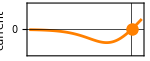

```mathematica
roots=SolveValues[Simplify[3/5 Subscript[f, NMDA][mVto[u mV]]==0],u,Reals];(*equilibria*)
Show[Plot[Evaluate[
-3/5 fNMDA[mVto[u mV]]
],{u,-100,10},
AspectRatio->1/(3/2 GoldenRatio),Frame->True,FrameLabel->{{"current", None}, {None,None}},FrameTicks->{{{0},None},{{{-90,None},{0,None}},None}},PlotRange->{{-100,10},{-0.35,0.35}},ImageSize->150,PlotStyle->RGBColor["#ff8000"],GridLines->{{0}},GridLinesStyle->Black],
Graphics[{RGBColor["#ff8000"],PointSize[0.06],Point[{#,0}]}]&/@roots
]
```

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Ai.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Ai.svg

#### Fig. 2Aii

KIR channels - voltage gating modeled with a sigmoid

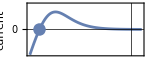

```mathematica
roots=SolveValues[Simplify[7/5 Subscript[f, KIR][mVto[u mV]]==0],u,Reals];
Show[Plot[Evaluate[
-7/5 Subscript[f, KIR][mVto[u mV]]
],{u,-100,10},
AspectRatio->1/(3/2 GoldenRatio),Frame->True,FrameLabel->{{"current", None}, {None,None}},FrameTicks->{{{0},None},{{{-90,None},{0,None}},None}},PlotRange->{{-100,10},{-0.35,0.35}},ImageSize->150,PlotStyle->RGBColor["#6580b1"],GridLines->{{0}},GridLinesStyle->Black],
Graphics[{RGBColor["#6580b1"],PointSize[0.06],Point[{#,0}]}]&/@roots
]
```

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Aii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Aii.svg

#### Fig. 2Aiii

Coactive NMDA and KIR channels

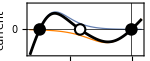

```mathematica
roots=SolveValues[Simplify[7/5 Subscript[f, KIR][mVto[u mV]]+3/5 Subscript[f, NMDA][mVto[u mV]]==0],u,Reals];
Show[
Plot[Evaluate[
{
- 7/5 Subscript[f, KIR][mVto[u mV]],
-3/5 Subscript[f, NMDA][mVto[u mV]],
-(7/5 Subscript[f, KIR][mVto[u mV]]+3/5 Subscript[f, NMDA][mVto[u mV]])
}],{u,-100,10},
AspectRatio->1/(3/2 GoldenRatio),Frame->True,FrameLabel->{{"current", None}, {None,None}},FrameTicks->{{{0},None},{None,None}},PlotRange->{{-100,10},{-0.35,0.35}},ImageSize->150,PlotStyle->{Directive[RGBColor["#6580b1"],Thickness[0.006]],Directive[RGBColor["#ff8000"],Thickness[0.006]],Black},GridLines->{{0}},GridLinesStyle->Black],
Graphics[{Black,PointSize[0.06],Point[{#,0}]}]&/@roots,
Graphics[{White,PointSize[0.04],Point[{#,0}]}]&/@roots[[2;;;;2]]
]
```

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Aiii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Aiii.svg

#### Fig. 2Aiv

Coactive voltage-gated depolarizing and hyperpolarizing channels - approximated with a cubic polynomial

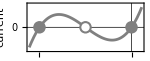

```mathematica
roots=SolveValues[Simplify[(𝒻[mVto[u mV]]==0)/.{𝓇->0}],u,Reals];
Show[Plot[Evaluate[{
-𝒻[mVto[u mV]]/.{𝓇->0}
}],{u,-100,10},
AspectRatio->1/(3/2 GoldenRatio),Frame->True,FrameLabel->{{"current", None}, {"voltage (mV)",None}},FrameTicks->{{{0},None},{{{-90,-90},{0,0}},None}},PlotRange->{{-100,10},{-0.35,0.35}},ImageSize->150,PlotStyle->{Gray},GridLines->{{0}},GridLinesStyle->Black],
Graphics[{Gray,PointSize[0.06],Point[{#,0}]}]&/@roots,
Graphics[{White,PointSize[0.04],Point[{#,0}]}]&/@roots[[2;;;;2]]
]
```

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Aiv.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Aiv.svg

### Fig. 3 IV curves:

Shows how localizing conductances to discrete synaptic sites changes the number of stable equilibria in the boundary segments. Neighbors are assumed to be at plateau (e_NMDA) and rest (e_KIR).

#### Helper code to plot the IV curves

```mathematica
plotIVu1[repval_(* rule for parameter assignment *)
]:=Module[{roots},
roots=SolveValues[Simplify[
(𝒻[mVto[u mV]]+ℓ^2(Subscript[e, NMDA]-mVto[u mV])/Δx^2+ℓ^2(Subscript[e, KIR]-mVto[u mV])/Δx^2==0)/.repval
],u,Reals];
Show[Plot[Evaluate[{
-𝒻[mVto[u mV]]/.repval,(* IV curve of an isolated segment*)
-(𝒻[mVto[u mV]]+ℓ^2(Subscript[e, NMDA]-mVto[u mV])/Δx^2+ℓ^2(Subscript[e, KIR]-mVto[u mV])/Δx^2)/.repval (* IV curve of a segment with a resting and plateauing neighbor*)
}],{u,-100,10},
AspectRatio->1/(3/2 GoldenRatio),Frame->True,FrameLabel->{{"current", None}, {"",None}},FrameTicks->{{{0},None},{{-90,0},None}},PlotRange->{{-100,10},{-0.35,0.35}},ImageSize->150,PlotStyle->{Directive[Gray,Thickness[0.006]],Brown},GridLines->{{1},{0}},GridLinesStyle->Black,Axes->False],
Graphics[{Brown,PointSize[0.06],Point[{#,0}]}]&/@roots,
Graphics[{White,PointSize[0.04],Point[{#,0}]}]&/@roots[[2;;;;2]]
]
]
```

#### Fig. 3Aii

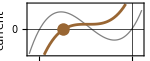

```mathematica
repval={𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR])/.{Subscript[G, KIR]->4/3 Subscript[G, NMDA]},Δx->2ℓ};
plotIVu1[repval]
```

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Aii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Aii.svg

#### Fig. 3Bii

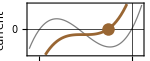

```mathematica
repval={𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR])/.{Subscript[G, KIR]->3/4 Subscript[G, NMDA]},Δx->2ℓ};
plotIVu1[repval]
```

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Bii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Bii.svg

#### Fig. 3Cii

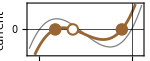

```mathematica
repval={𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR])/.{Subscript[G, KIR]->3/4 Subscript[G, NMDA]},Δx->3ℓ};
plotIVu1[repval]
```

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Cii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Cii.svg

### Fig. 4 IV curves

Shows how increasing synaptic spacing changes the local stability structure from one stable equilibrium to three and then four. Provides the one-dimensional current plots that are cross sections of phase portraits.

#### Thevenin equivalent conductances: g_dis, g_prx

The Thevenin equivalent conductance G_∞ for a long dendrite with membrane conductance G_Ch

```mathematica
Subscript[𝒢, ∞soln]=Simplify[Solve[1/Subscript[G, ∞]==Subscript[R, s]+1/(Subscript[G, Ch]+Subscript[G, ∞]), Subscript[G, ∞]],{Subscript[G, Ch]>0}][[2]][[1]]
```

G_∞→1/2 (-G_Ch+(√(G_Ch (4+G_Ch R_s)))/(√R_s))

For the proximal side, with the dendrite mainly at rest and thus KIR channels dominating (G_Ch=G_KIR)

```mathematica
Subscript[G, prx]=FullSimplify[Subscript[G, ∞]/. Subscript[𝒢, ∞soln]/.{Subscript[G, Ch]-> Subscript[G, KIR]},Subscript[R, s]>0]
```

1/2 (-G_KIR+√(G_KIR (G_KIR+4/R_s)))

For the distal side, with the dendrite mainly at plateau and thus NMDA channels dominating (G_Ch=G_NMDA)

```mathematica
Subscript[G, dis]=FullSimplify[Subscript[G, ∞]/. Subscript[𝒢, ∞soln]/.{Subscript[G, Ch]-> Subscript[G, NMDA]},Subscript[R, s]>0]
```

1/2 (-G_NMDA+√(G_NMDA (G_NMDA+4/R_s)))

Converting from units of G_NMDA, G_KIR, and R_s to units of (Δx/ℓ), G_c, and 𝓇=Δ𝒢_c/(2 𝒢_c).

```mathematica
ChGtoGcr=Simplify@Solve[{Subscript[G, c]==(Subscript[G, NMDA]+Subscript[G, KIR])/2,𝓇==(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR])},{Subscript[G, NMDA],Subscript[G, KIR]}][[1]]
```

{G_NMDA→(1+𝓇) G_c,G_KIR→-((-1+𝓇) G_c)}

```mathematica
Rstoℓr=Solve[1/(Subscript[R, s] Subscript[G, c])==(ℓ/Δx)^2,Subscript[R, s]][[1]]
```

{R_s→Δx^2/(ℓ^2 G_c)}

Normalizing by G_c

```mathematica
Subscript[g, prx]=FullSimplify[Subscript[G, prx]/Subscript[G, c]/.ChGtoGcr/.Rstoℓr,Subscript[G, c]>0]
```

1/2 (-1+𝓇+√((-1+𝓇) (-1+𝓇-(4 ℓ^2)/Δx^2)))

```mathematica
Subscript[g, dis]=FullSimplify[Subscript[G, dis]/Subscript[G, c]/.ChGtoGcr/.Rstoℓr,Subscript[G, c]>0]
```

1/2 (-1-𝓇+√((1+𝓇) (1+𝓇+(4 ℓ^2)/Δx^2)))

#### Helper code to plot the IV curves

```mathematica
plotIVu1Thev[repval_]:=Module[{roots},
roots=SolveValues[Simplify[((1-𝓇)Subscript[f, KIR][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]]+Subscript[g, dis](Subscript[e, NMDA]-mVto[u mV])+ℓ^2(Subscript[e, KIR]-mVto[u mV])/Δx^2==0)/.repval],u,Reals];
Show[Plot[Evaluate[{
-((1-𝓇)Subscript[f, KIR][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]])/.repval,
-((1-𝓇)Subscript[f, KIR][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]]+Subscript[g, dis](Subscript[e, NMDA]-mVto[u mV])+ℓ^2(Subscript[e, KIR]-mVto[u mV])/Δx^2
)/.repval
}],{u,-100,10},
AspectRatio->1/(3/2 GoldenRatio),Frame->True,FrameLabel->{{"current", None}, {"",None}},FrameTicks->{{{0},None},{{-90,0},None}},PlotRange->{{-100,10},{-0.4,0.4}},ImageSize->125,PlotStyle->{Directive[Black,Thickness[0.006]],Brown,Black},GridLines->{{0}},GridLinesStyle->Black],
Graphics[{Brown,PointSize[0.06],Point[{#,0}]}]&/@roots,
Graphics[{White,PointSize[0.04],Point[{#,0}]}]&/@roots[[2;;;;2]]
]
]
```

```mathematica
plotIVu2Thev[repval_]:=Module[{roots},
roots=SolveValues[Simplify[((1-𝓇)Subscript[f, KIR][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]]+ℓ^2(Subscript[e, KIR]-mVto[u mV])/Δx^2+Subscript[g, prx](Subscript[e, KIR]-mVto[u mV])==0)/.repval],u,Reals];
Show[Plot[Evaluate[{
-((1-𝓇)Subscript[f, KIR][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]])/.repval,
-((1-𝓇)Subscript[f, KIR][mVto[u mV]]+(1+𝓇)Subscript[f, NMDA][mVto[u mV]]+ℓ^2(Subscript[e, KIR]-mVto[u mV])/Δx^2+Subscript[g, prx](Subscript[e, KIR]-mVto[u mV])
)/.repval
}],{u,-100,10},
AspectRatio->1/(3/2 GoldenRatio),Frame->True,FrameLabel->{{"current", None}, {"",None}},FrameTicks->{{{0},None},{{-90,0},None}},PlotRange->{{-100,10},{-0.4,0.4}},ImageSize->125,PlotStyle->{Directive[Black,Thickness[0.006]],Purple,Black},GridLines->{{0}},GridLinesStyle->Black],
Graphics[{Purple,PointSize[0.06],Point[{#,0}]}]&/@roots,
Graphics[{White,PointSize[0.04],Point[{#,0}]}]&/@roots[[2;;;;2]]
]
]
```

#### Fig. 4Ai

```mathematica
repval={𝓇->-6/10,Δx->2ℓ};
plotIVu1Thev[repval]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Ai.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Ai.svg

#### Fig. 4Aii

```mathematica
repval={𝓇->-6/10,Δx->2ℓ};
plotIVu2Thev[repval]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Aii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Aii.svg

#### Fig. 4Bi

```mathematica
repval={𝓇->-4/10,Δx->2.5ℓ};
plotIVu1Thev[repval]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Bi.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Bi.svg

#### Fig. 4Bii

```mathematica
repval={𝓇->-4/10,Δx->2.5ℓ};
plotIVu2Thev[repval]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Bii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Bii.svg

#### Fig. 4Ci

```mathematica
repval={𝓇->-3/10,Δx->4ℓ};
plotIVu1Thev[repval]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Ci.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Ci.svg

#### Fig. 4Cii

```mathematica
repval={𝓇->-3/10,Δx->4ℓ};
plotIVu2Thev[repval]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Cii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Cii.svg

## Channels distributed along a dendrite

#### Fig. 2Bi

```mathematica
repval={𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR])/.{Subscript[G, NMDA]->1 Subscript[G, KIR]},Subscript[G, AMPA]->25 Subscript[𝒢, c] ℓ,τA->2,τ->1,ℓ->1};
uinit[x_]:=-1;
diffeq=Hold[
τ D[u[x,t], t]==𝒻[u[x,t]]+ℓ^2 D[u[x,t], x,x]+Subscript[G, AMPA]/(Subscript[𝒢, c] ℓ)δ[0.1][x] Subscript[f, AMPA][u[x,t],t,τA,40]
];

ndsol=NDSolve[
{
ReleaseHold[diffeq],
u[x,-20]==uinit[x],
u[-30,t]==-1,u[30,t]==-1
}//.repval,
u[x,t],{x,-30,30},{t,-20,160},
MaxStepSize->0.01];


Show[Plot3D[Evaluate[u[x,t]/. ndsol],{x,-15,15},{t,0,160},AxesLabel->{"","",""},Axes->True,PlotRange->All,PlotPoints->100,Mesh->{Range[-30,30,5],Range[-0.3,160,20]},ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Ticks->{{#,""}&/@Range[-30,30,5],{#,""}&/@Range[0,160,20],{{-1,-90},{1,0}}},ImageSize->200,AxesEdge->{{-1,-1},{-1,1},{-1,-1}}],
ListPointPlot3D[{{0,40,1}},PlotStyle->{Red,PointSize[0.02]}]]
```

-Graphics3D-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Ci.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Ci.png

#### Fig. 2Bii

```mathematica
repval={𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR])/.{Subscript[G, NMDA]->1 Subscript[G, KIR]},Subscript[G, AMPA]->25 Subscript[𝒢, c] ℓ,Subscript[G, AMPA]->25 Subscript[𝒢, c] ℓ,τA->2,τ->1,ℓ->1};
uinit[x_]:=-1;
diffeq=Hold[
τ D[u[x,t], t]==𝒻[u[x,t]]+ℓ^2 D[u[x,t], x,x]+Subscript[G, AMPA]/(Subscript[𝒢, c] ℓ)(δ[0.1][x]+δ[0.1][x+5]) Subscript[f, AMPA][u[x,t],t,τA,40]
];

ndsol=NDSolve[
{
ReleaseHold[diffeq],
u[x,-20]==uinit[x],
u[-30,t]==-1,u[30,t]==-1
}//.repval,
u[x,t],{x,-30,30},{t,-20,160},
MaxStepSize->0.01];


Show[Plot3D[Evaluate[u[x,t]/. ndsol],{x,-15,15},{t,0,160},AxesLabel->{"","",""},Axes->True,PlotRange->All,PlotPoints->100,Mesh->{Range[-30,30,5],Range[-0.3,160,20]},ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Ticks->{{#,""}&/@Range[-30,30,5],{#,""}&/@Range[0,160,20],{{-1,-90},{1,0}}},ImageSize->200,AxesEdge->{{-1,-1},{-1,1},{-1,-1}}],
ListPointPlot3D[{{0,40,1},{-5,40,1}},PlotStyle->{Red,PointSize[0.02]}]]
```

-Graphics3D-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Cii.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Cii.png

#### Fig. 2Ci

```mathematica
repval={𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR])/.{Subscript[G, NMDA]->3/4 Subscript[G, KIR]}};
uinit[x_]:=-Tanh[(x-.5)/(2 ℓ) ];
diffeq=Hold[
τ D[u[x,t], t]==𝒻[u[x,t]]+ℓ^2 D[u[x,t], x,x]
];

ndsol=NDSolve[{ReleaseHold[diffeq],
u[x,-20]==uinit[x],
u[-30,t]==1,u[30,t]==-1
}/.repval/.{ℓ->1,τ->1},
u[x,t],{x,- 30,30},{t,-20,160},
MaxStepSize->0.1];

Show[Plot3D[Evaluate[u[x,t]/. ndsol],{x,-15,15},{t,0,160},AxesLabel->{"","",""},Axes->True,PlotRange->All,PlotPoints->100,Mesh->{Range[-15,15,5],Range[0,160,20]},ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Ticks->{{#,""}&/@Join[Range[-5,-15,-5],Range[0,15,5]],{#,""}&/@Range[0,160,20],{{-1,""},{1,""}}},ImageSize->200,AxesEdge->{{-1,-1},{-1,1},{-1,-1}}]]
```

-Graphics3D-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Bi.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Bi.png

#### Fig. 2Cii

```mathematica
repval={𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR])/.{Subscript[G, NMDA]->1 Subscript[G, KIR]}};
uinit[x_]:=-Tanh[(x-.5)/(2 ℓ) ];
diffeq=Hold[
τ D[u[x,t], t]==𝒻[u[x,t]]+ℓ^2 D[u[x,t], x,x]
];

ndsol=NDSolve[{ReleaseHold[diffeq],
u[x,-20]==uinit[x],
u[-30,t]==1,u[30,t]==-1
}/.repval/.{ℓ->1,τ->1},
u[x,t],{x,- 30,30},{t,-20,160},
MaxStepSize->0.1];

Show[Plot3D[Evaluate[u[x,t]/. ndsol],{x,-15,15},{t,0,160},AxesLabel->{"","",""},Axes->True,PlotRange->All,PlotPoints->100,Mesh->{Range[-15,15,5],Range[0,160,20]},ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Ticks->{{#,""}&/@Join[Range[-5,-15,-5],Range[0,15,5]],{#,""}&/@Range[0,160,20],{{-1,""},{1,""}}},ImageSize->200,AxesEdge->{{-1,-1},{-1,1},{-1,-1}}]]
```

-Graphics3D-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Bii.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig2Bii.png

## Channels localized to synapses

### Channels modeled with a cubic

Uses the cubic approximation to expose the basic mechanism of retreat, advance, and anchoring. Provides the minimal model underlying the Fig. 3A–D simulations.

#### Simulating dendrite voltage with channels modelled with a cubic

```mathematica
checkDriftCubic[repval_,plot_:False,offset_:0]:=Module[
{nN,xs,vars,uinit,eqs,tlim,ndsol},
nN=If[((Δx/ℓ)^2//.repval)>4,10,20];(*nN is half the number of synapses on the dendrite. 
Modeling a longer dendrite when x spacing when synapses are close together. 
nN chosen to be large enough that increasing it doesn't affect the resulting behavior*)
xs=Range[-nN,nN];
vars=Table[u[i][t],{i,-nN,nN}];
uinit[x_]:=-Tanh[(x+offset)/(2 ℓ) ];(*Initial conditions*)
(*build ODEs*)
eqs=Table[
τ u[i]'[t]==𝒻[u[i][t]]+
(ℓ/Δx)^2 ((If[i<nN,u[i+1][t],u[i][t]]+If[i>-nN,u[i-1][t],u[i][t]])-2  u[i][t])(*Closed boundary conditions*)
,{i,-nN,nN}
];

tlim=50;
ndsol=NDSolve[Flatten@{
eqs,
Table[u[i][-20]==uinit[xs[[i+nN+1]]Δx],{i,-nN,nN}]
}//.repval,vars,{t,-20,tlim},
MaxStepSize->0.1];

(* plot voltage over position and time *)
If[plot,Show[ListPlot3D[Flatten[Table[{xs[[i+nN+1]],t,(u[i][t]/. ndsol)[[1]]},{i,-2,2},{t,0,tlim,1}],1],Mesh->{Range[-nN,nN,1],Range[0,tlim,10]},PlotRange->{{-2,2 },All,{-1.01,1.01}},AxesLabel->None,ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Axes->True,ImageSize->200, Ticks->{{#,""}&/@Range[-nN,nN,1],{#,""}&/@Range[0,tlim,10],{{-1,""},{1,""}}}]]//Print
];

(*If the plateau has retreated (r) or advanced (p) throughout the dendrite return accordingly *)
If[(u[-nN][t]/. ndsol/. {t->tlim})[[1]]<0,Return[r]];If[(u[nN][t]/. ndsol/. {t->tlim})[[1]]>0,Return[p]];

(*Else, if the front is drifting, infer the direction and return accordingly, otherwise return s*)
rmax=MaximalBy[
Evaluate@Table[(u[i][t]/. ndsol/. {t->tlim})[[1]],{i,-nN,nN}]-Evaluate@Table[(u[i][t]/. ndsol/. {t->0.75tlim})[[1]],{i,-nN,nN}],
Abs
][[1]];
If[rmax>0.1, p,
If[rmax<-0.1,r,s]]

]
```

#### Fig. 3Ai: Boundary drift - plateau retreats

```mathematica
repval={𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR])/.{Subscript[G, KIR]->4/3 Subscript[G, NMDA]},Δx->2ℓ,τ->1};
checkDriftCubic[repval,True,-3ℓ]
```

-Graphics3D-

r

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Ai.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Ai.png

#### Fig. 3Bi: Boundary drift - plateau advances

```mathematica
repval={𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR])/.{Subscript[G, KIR]->3/4 Subscript[G, NMDA]},Δx->2ℓ,τ->1};
checkDriftCubic[repval,True,3ℓ]
```

-Graphics3D-

p

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Bi.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Bi.png

#### Fig. 3Ci: Boundary anchored

```mathematica
repval={𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR])/.{Subscript[G, KIR]->3/4 Subscript[G, NMDA]},Δx->3ℓ,τ->1};
checkDriftCubic[repval,True,1ℓ]
```

-Graphics3D-

s

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Ci.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3Ci.png

#### Fig. 3D: Sweeping parameters - voltage gating modeled as a cubic

```mathematica
{vals3o,coords3o}=theCut[checkDriftCubic[{Δx->√#1 ℓ,𝓇->#2,τ->0.01},False,0.5Δx]&,{{RsGc,0.1,20},{𝓇,-1,1}},4,(*minDepth*)8,(*maxDepth*){p,r,s}];
plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,20},{𝓇,-1,1}},{p,r,s},{White,White,LightGray},{Dotted,Thick}]
```

2

3

4

5

6

7

8

-Graphics-

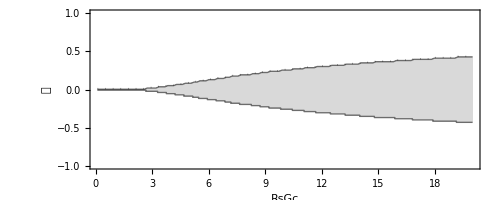
```mathematica
ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
Show[-Graphics-,ListPlot[{{4,1/7},{9,1/7},{4,-1/7}},PlotStyle->Black],GridLines->{{},{0}},Method->{"GridLinesInFront"->True},GridLinesStyle->{Gray},FrameTicks->{{{-1,0,1},None},{ticksBaseSlnt,ticksSqrt}},ImageSize->250,AspectRatio->1/2,FrameLabel->{"", ""},PlotRange->{{0,20},{-1,1}},Frame->True,PlotRangePadding->0]
```

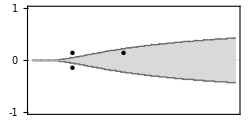

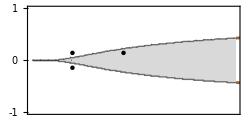
```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3D.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3D.png

### Channels modeled with a sigmoid

Repeats the anchoring analysis with sigmoidal NMDA and KIR voltage dependence. Shows that the same spacing-dependent anchoring persists, with the anchoring minimum shifted by the asymmetry of the two channel nonlinearities.

#### Simulating dendrite voltage with channels modelled with a sigmoid

Simulates a dendrite with NMDA and KIR channels localized to synapses (when m is 1), or with KIR channels distributed to m compartments between localized NMDA synapses.

```mathematica
checkDriftSig[repval_,
m_,(*number of compartments between adjacent synapses*)
plot_:False,offset_:0]:=Module[
{nN,nm,xs,vars,uinit,eqs,tlim,ndsol,rmax},
nN=If[((Δx/ℓ)^2//.repval)>4,10,20];
nm=nN m+Floor[m/2];
xs=Range[-nm,nm];
vars=Table[u[i][t],{i,-nm,nm}];
uinit[x_]:=-(2UnitStep[(x+offset)/(2 ℓ)]-1); (*Initial conditions*)
(*build ODEs*)
eqs=Table[
τ u[i]'[t]==
If[Mod[i,m]==0,m(1+𝓇)Subscript[f, NMDA][u[i][t]],0](*NMDA channels in every mth compartment*)
+(1-𝓇)Subscript[f, KIR][u[i][t]] (*KIR channels in every compartment*)+
m^2(ℓ/Δx)^2(If[i<nm,u[i+1][t],u[i][t]]+If[i>-nm,u[i-1][t],u[i][t]]-2  u[i][t])(*Closed boundary conditions*)
,{i,-nm,nm}
];
tlim=50;
ndsol=NDSolve[Flatten@{
eqs,
Table[u[i][-20]==uinit[xs[[i+nm+1]] Δx/m],{i,-nm,nm}]
}//.repval,vars,{t,-20,tlim},MaxStepSize->0.1];
If[plot,Show[ListPlot3D[Flatten[Table[{xs[[i+nm+1]],t,(u[i][t]/. ndsol)[[1]]},{i,-(2m+Floor[m/2]),(2m+Floor[m/2])},{t,-20,tlim,1}],1],Mesh->{Range[-2m,2m,m],Range[0,tlim,10]},PlotRange->{{-2m,2 m},All,{-1.01,1.01}},AxesLabel->None,ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Axes->True,ImageSize->200, Ticks->{{#,""}&/@Range[-2m,2m,m],{#,""}&/@Range[0,tlim,10],{{-1,""},{1,""}}}]]//Print
];

If[(u[-nm][t]/. ndsol/. {t->tlim})[[1]]<0,Return[r]];If[(u[nm][t]/. ndsol/. {t->tlim})[[1]]>0,Return[p]];

rmax=MaximalBy[
Evaluate@Table[(u[i][t]/. ndsol/. {t->tlim})[[1]],{i,-nm,nm}]-Evaluate@Table[(u[i][t]/. ndsol/. {t->0.75tlim})[[1]],{i,-nm,nm}],
Abs
][[1]];

If[rmax>0.1, p,
If[rmax<-0.1,r,s]]
]
```

NMDA and KIR channels localized to synapses:

```mathematica
repval={𝓇->-0.6,Δx->5ℓ,τ->1};
checkDriftSig[repval,1,True,0.5Δx]
```

-Graphics3D-

s

NMDA channels localized to synapses with KIR channels distributed to m=10 compartments between each pair.

```mathematica
repval={𝓇->-0.6,Δx->5ℓ,τ->1};
checkDriftSig[repval,10,True,0.5Δx]
```

-Graphics3D-

s

#### Fig. 3E: Sweeping parameters - NMDA and KIR channels modeled with a sigmoid

```mathematica
{vals3o,coords3o}=theCut[checkDriftSig[{Δx->√#1 ℓ,𝓇->#2,τ->0.01},1,False,0.5Δx]&,{{RsGc,0.1,20},{𝓇,-1,1}},4,(*minDepth*)8,(*maxDepth*){p,r,s}];
plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,20},{𝓇,-1,1}},{p,r,s},{White,White,LightGray},{Dotted,Thick}]
```

2

3

4

5

6

7

8

-Graphics-

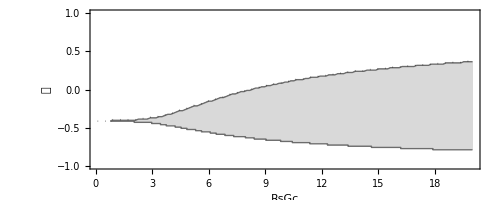
```mathematica
ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];

Show[-Graphics-,PlotStyle->Black,GridLines->{{},{0}},Method->{"GridLinesInFront"->True},GridLinesStyle->{Gray},FrameTicks->{{{-1,0,1},None},{ticksBaseSlnt,ticksSqrtSlnt}},ImageSize->250,AspectRatio->1/2,FrameLabel->{"", ""},PlotRange->{{0,20},{-1,1}},Frame->True,PlotRangePadding->0]
```

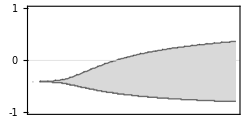

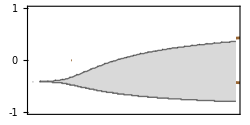
```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3E.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3E.png

#### Fig. 3F: Sweeping parameters - KIR channels distributed along the dendrite

```mathematica
{vals3o,coords3o}=theCut[checkDriftSig[{Δx->√#1 ℓ,𝓇->#2,τ->0.01},10,False,0.5Δx]&,{{RsGc,0.1,20},{𝓇,-1,1}},4,(*minDepth*)8,(*maxDepth*){p,r,s}];
plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,20},{𝓇,-1,1}},{p,r,s},{White,White,LightGray},{Dotted,Thick}]
```

2

3

4

5

6

7

8

-Graphics-

```mathematica
ticksSqrt=Table[{i^2,If[Mod[i,1]==0∧i!=1,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];

Show[-Graphics-,GridLines->{{},{0}},Method->{"GridLinesInFront"->True},GridLinesStyle->{Gray},FrameTicks->{{{-1,0,1},None},{{0,10,20},ticksSqrtSlnt}},ImageSize->250,FrameLabel->{"", ""},Frame->True,PlotRangePadding->0,ImageSize->250,AspectRatio->1/2]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3F.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig3F.png

### AMPA inputs advancing the plateau

Tests when transient AMPA input advances an anchored front forward. Shows that order selectivity requires AMPA conductance strong enough to recruit the adjacent site but not so strong that it also recruits the more distant one.

#### Simulating dendrite voltage with channels modelled with a sigmoid with AMPA inputs

```mathematica
checkAdvanceSig[𝒯_ (* list of times at which snapses ahead of the front receive an AMPA input*)
][repval_,m_,plot_:False,offset_:0,redDotHeight_:1]:=Module[
{n,nN,nm,rnm,xs,vars,uinit,eqs,tlim,ndsol,rmax,redDotHeightv},
n=Length[𝒯];
nN=If[((Δx/ℓ)^2/.repval)>4,10,20];
nm=nN m+Floor[m/2];
rnm=n m +nm;
xs=Range[-nm,rnm];
vars=Table[u[i][t],{i,-nm,rnm}];
uinit[x_]:=-(2UnitStep[(x+offset)/(2 ℓ)]-1);
(*build ODEs*)
eqs=Table[
τ u[i]'[t]==
If[Mod[i,m]==0,m((1+𝓇)Subscript[f, NMDA][u[i][t]]+
If[1<=i/m<=n,Subscript[G, AMPA]/Subscript[G, c] Subscript[f, AMPA][u[i][t],t,τA,𝒯[[i/m]]],0]
 ),0]+(1-𝓇)Subscript[f, KIR][u[i][t]]+
m^2(ℓ/Δx)^2(If[i<rnm,u[i+1][t],u[i][t]]+If[i>-nm,u[i-1][t],u[i][t]]-2  u[i][t])(*Closed boundary conditions*)
,{i,-nm,rnm}
];
tlim=Max[𝒯]+If[n>1,2Abs[𝒯[[2]]-𝒯[[1]]],20];
ndsol=NDSolve[Flatten@{
eqs,
Table[u[i][-20]==uinit[xs[[i+nm+1]] Δx/m],{i,-nm,rnm}]
}//.repval,vars,{t,-20,tlim}];
If[plot,
redDotHeightv=redDotHeight;
If[redDotHeight==1,redDotHeightv={1,1}];

Print[redDotHeightv];Show[ListPlot3D[Flatten[Table[{xs[[i+nm+1]],t,(u[i][t]/. ndsol)[[1]]},{i,-(m+Floor[m/2]),(n m+2m+Floor[m/2])},{t,0,tlim,τ/.repval}],1],Mesh->{Range[-m,n m +2m,m],Range[0,tlim,Abs[𝒯[[2]]-𝒯[[1]]]]},PlotRange->{{-m,n m +2m},All,{-1.01,1.01}},AxesLabel->None,ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Axes->True,ImageSize->200, Ticks->{{#,""}&/@Range[-2,5,1],{#,""}&/@Range[0,120,40],{{-1,""},{1,""}}},AxesEdge->{{-1,-1},{-1,1},{-1,-1}}],
ListPointPlot3D[Table[{i,𝒯[[i]]+2τA/.repval,redDotHeightv[[i]]},{i,Range[Length[𝒯]]}],PlotStyle->{Red,PointSize[0.02]}]
]//Print
];
(*If the plateau has retreated or advanced throughout the dendrite return False or True respectively *)
If[(u[-nm][t]/. ndsol/. {t->tlim})[[1]]<0,Return[False]];If[(u[nm][t]/. ndsol/. {t->tlim})[[1]]>0,Return[True]];

(*Else, return whether the plateau has advanced after the inputs arrived vs just before the first input*)
(u[n m][t]/. ndsol/.{t->tlim})[[1]]>(1/10(9(u[0][t]/. ndsol/.{t->Min[𝒯]-1})[[1]]+1(u[m][t]/. ndsol/.{t->Min[𝒯]-1})[[1]]))
]
```

#### Fig. 5Ai

```mathematica
repval={𝓇->-0.4,Δx->2.5ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};
checkAdvanceSig[{40,80}][repval,1,True,-0.5Δx,{0.7,0.7}]
```

{0.7,0.7}

-Graphics3D-

True

```mathematica
Show[-Graphics3D-,Ticks->{{#,""}&/@Range[-2,5,1],{#,""}&/@Range[0,120,40],{{-1,"-90"},{1,"0"}}},AxesEdge->{{-1,-1},{-1,1},{-1,-1}}]
```

-Graphics3D-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Ai.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Ai.png

#### Fig. 5Aiii

```mathematica
repval={𝓇->-0.4,Δx->2.5ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};
checkAdvanceSig[{80,40}][repval,1,True,-0.5Δx,{0.7,-0.6}]
```

{0.7,-0.6}

-Graphics3D-

False

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Aiii.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Aiii.png

#### Fig. 5Bi

```mathematica
repval={𝓇->-0.4,Δx->2.5ℓ,Subscript[G, AMPA]->0.375 Subscript[G, c],τA->2,τ->1};
checkAdvanceSig[{80,40}][repval,1,True,-0.5Δx,{0.8,0.0}]
```

{0.8,0.}

-Graphics3D-

False

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Bi.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Bi.png

#### Fig. 5Biii

```mathematica
repval={𝓇->-0.4,Δx->2.5ℓ,Subscript[G, AMPA]->0.5 Subscript[G, c],τA->2,τ->1};
checkAdvanceSig[{80,40}][repval,1,True,-0.5Δx,{1,0.5}]
```

{1,0.5}

-Graphics3D-

True

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Biii.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Biii.png

#### Fig. 5Ci

```mathematica
repval={𝓇->-0.3,Δx->4ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};
checkAdvanceSig[{80,40}][repval,1,True,-0.5Δx,{0.9,-0.55}]
```

{0.9,-0.55}

-Graphics3D-

False

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Ci.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Ci.png

#### Fig. 5Ciii

```mathematica
repval={𝓇->-0.3,Δx->4ℓ,Subscript[G, AMPA]->0.5 Subscript[G, c],τA->2,τ->1};
checkAdvanceSig[{80,40}][repval,1,True,-0.5Δx,{1,0.8}]
```

{1,0.8}

-Graphics3D-

True

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Ciii.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Ciii.png

## Phase Portraits

```mathematica
phasePortraits[𝒯_][repval_]:=Module[{urangex,urangey,rhs1,rhs2,rawSols,pts,uniquePts,sols,J,nc,ptsGraphics,saddleU,saddleS,fieldPlot,sepPts,sepPlot,eq1,eq2,solns,pp1,pp2,𝒯v},
urangex={-1.3,1.3};
urangey={-1.3,1.3};

rhs1=(1+𝓇)Subscript[f, NMDA][u[1][t]]+(1-𝓇)Subscript[f, KIR][u[1][t]]+Subscript[g, dis](Subscript[e, NMDA]-u[1][t])+(ℓ/Δx)^2(u[2][t]-u[1][t]);
rhs2=(1+𝓇)Subscript[f, NMDA][u[2][t]]+(1-𝓇)Subscript[f, KIR][u[2][t]]+(ℓ/Δx)^2(u[1][t]-u[2][t])+Subscript[g, prx](Subscript[e, KIR]-u[2][t]);

rawSols=Quiet[FindRoot[Evaluate[{rhs1==0,rhs2==0}/.repval],{{u[1][t],#[[1]]},{u[2][t],#[[2]]}}]&/@Flatten[Table[{i,j},{i,-1,1,1},{j,-1,1,1}],1]];

rawSols=Select[rawSols,((rhs1^2+rhs2^2<0.0001)/. repval/.#)&];

pts=({u[1][t],u[2][t]}/.rawSols)//N;

uniquePts=DeleteDuplicates[pts,EuclideanDistance[#1,#2]<0.1&];

sols=(Thread[{u[1][t],u[2][t]}->#]&/@uniquePts);

J=D[{rhs1,rhs2},{{u[1][t],u[2][t]}}];
nc=ContourPlot[Evaluate[{rhs2==0,rhs1==0}/.repval],{u[2][t], urangex[[1]],urangex[[2]]},{u[1][t], urangey[[1]],urangey[[2]]},ContourStyle->{Directive[Lighter[Purple],Thickness[0.004]],Directive[Lighter[Brown],Thickness[0.004]]}];

ptsGraphics=Graphics[Table[Module[{pt={u[2][t],u[1][t]}/. sol,Jpt,evals},Jpt=J/. {u[2][t]->pt[[1]],u[1][t]->pt[[2]]}/. repval;
evals=Eigenvalues[Jpt];
If[AllTrue[evals,#<0&],(*stable:filled black dot*){Black,PointSize[Large],Point[pt]},(*unstable:open dot=black then smaller white*){Black,PointSize[Large],Point[pt],White,PointSize[Medium],Point[pt]}]],{sol,sols}]];

fieldPlot=StreamPlot[Evaluate[{rhs2,rhs1}/. repval],{u[2][t],urangex[[1]],urangex[[2]]},{u[1][t],urangey[[1]],urangey[[2]]},StreamStyle->LightGray,StreamColorFunction->None,StreamScale->0.25,StreamPoints->75];


(*---separatrix seed points from saddle eigenvectors---*)sepPts=Module[{tol=10^-8,eps=0.2,saddles,classifyPt},classifyPt[sol_]:=Module[{pt,Jpt,evals,evecs,pos,neg,vu,vs},pt={u[1][t],u[2][t]}/. sol//N;
Jpt=(J/. Thread[{u[1][t],u[2][t]}->pt]/. repval)//N;
{evals,evecs}=Eigensystem[Jpt];
pos=Flatten@Position[evals,_?(Re[#]>tol&)];
neg=Flatten@Position[evals,_?(Re[#]<-tol&)];
If[Length[pos]==1&&Length[neg]==1,vu=Normalize[evecs[[pos[[1]]]]];
vs=Normalize[evecs[[neg[[1]]]]];
{pt+eps vs,pt-eps vs},Nothing]];
saddles=Flatten[classifyPt/@sols,1];saddles=({#[[2]],#[[1]]}&)/@saddles;DeleteDuplicates[saddles,EuclideanDistance[#1,#2]<10^-5&]];


sepPlot=StreamPlot[Evaluate[{rhs2,rhs1}/. repval],{u[2][t],urangex[[1]],urangex[[2]]},{u[1][t],urangey[[1]],urangey[[2]]},StreamPoints->{sepPts},StreamStyle->Directive[Cyan,Thickness[0.006]],StreamStyle->Directive[Cyan,Thickness[0.006]],StreamColorFunction->None,StreamScale->None,PlotRange->{urangex,urangey}];

Show[fieldPlot,sepPlot,nc,ptsGraphics,PlotRange->All,Frame->True,FrameLabel->{{"u_1",None},{"u_2",None}},FrameTicks->{{{{-1,-90},{1,0}},None},{{{-1,-90},{1,0}},None}},ImageSize->150]//Print;

𝒯v=𝒯;
eq1=τ D[u[1][t], t]==rhs1+Subscript[G, AMPA]/Subscript[G, c] Subscript[f, AMPA][u[1][t],t,τA,𝒯v[[1]]];
eq2=τ D[u[2][t], t]==rhs2+Subscript[G, AMPA]/Subscript[G, c] Subscript[f, AMPA][u[2][t],t,τA,𝒯v[[2]]];

solns=NDSolve[{
eq1,eq2,
u[1][0]==-1,u[2][0]==-1
}//.repval,
{u[1],u[2]},{t,0,Max[𝒯v]+Min[𝒯v]}];
pp1=ParametricPlot[{u[2][t],u[1][t]}/.solns,{t,𝒯v[[1]],𝒯v[[1]]+Abs[𝒯v[[1]]-𝒯v[[2]]]},PlotRange->{{urangex[[1]],urangex[[2]]},{urangey[[1]],urangey[[2]]}},PlotStyle->Directive[Thickness[0.008],Brown]];
pp2=ParametricPlot[{u[2][t],u[1][t]}/.solns,{t,𝒯v[[2]],𝒯v[[2]]+Abs[𝒯v[[1]]-𝒯v[[2]]]},PlotRange->{{urangex[[1]],urangex[[2]]},{urangey[[1]],urangey[[2]]}},PlotStyle->Directive[Thickness[0.008],Purple]];

Show[fieldPlot,sepPlot,nc,pp1/. Line[x_]:>{Arrowheads[{0.,0.08,0,0.08,0.0}],Arrow[x]},pp2/. Line[x_]:>{Arrowheads[{0.,0.08,0,0.08,0.0}],Arrow[x]},ptsGraphics,PlotRange->All,Frame->True,FrameLabel->{{"u_1",None},{"u_2",None}},FrameTicks->{{{{-1,-90},{1,0}},None},{{{-1,-90},{1,0}},None}},ImageSize->150]//Print;
]
```

#### Fig. 4Aiii

```mathematica
repval={𝓇->-0.6,Δx->2ℓ,Subscript[G, AMPA]->0.4 Subscript[G, c],τA->2,τ->1};
phasePortraits[{40,80}][repval]
```

-Graphics-

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Aiii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Aiii.svg

#### Fig. 4Biii and Fig. 5Aii

In-order inputs, AMPA conductance in order-selective range

```mathematica
repval={𝓇->-0.4,Δx->2.5ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};
phasePortraits[{40,80}][repval]
```

-Graphics-

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Biii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Biii.svg

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Aii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Aii.svg

#### Fig. 5Aiv

Out-of-order inputs, AMPA conductance in order-selective range

```mathematica
repval={𝓇->-0.4,Δx->2.5ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};
phasePortraits[{80,40}][repval]
```

Part::pspec1: Part specification NotFound is not applicable.

-Graphics-

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Aiv.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Aiv.svg

#### Fig. 5Bii

Out-of-order inputs, higher AMPA conductance crosses near separatrix

```mathematica
repval={𝓇->-0.4,Δx->2.5ℓ,Subscript[G, AMPA]->0.375 Subscript[G, c],τA->2,τ->1};
phasePortraits[{80,40}][repval]
```

Part::pspec1: Part specification NotFound is not applicable.

-Graphics-

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Bii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Bii.svg

#### Fig. 5Biv

Out-of-order inputs, too-higher AMPA conductance crosses near and far separatrix

```mathematica
repval={𝓇->-0.4,Δx->2.5ℓ,Subscript[G, AMPA]->0.5 Subscript[G, c],τA->2,τ->1};
phasePortraits[{80,40}][repval]
```

Part::pspec1: Part specification NotFound is not applicable.

-Graphics-

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Biv.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Biv.svg

#### Fig. 4Ciii and 5Cii

Out-of-order inputs, AMPA conductance in order-selective range

```mathematica
repval={𝓇->-0.3,Δx->4ℓ,Subscript[G, AMPA]->0.2 Subscript[G, c],τA->2,τ->1};
phasePortraits[{80,40}][repval]
```

Part::pspec1: Part specification NotFound is not applicable.

-Graphics-

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Ciii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4Ciii.svg

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Cii.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Cii.svg

#### Fig. 5Civ

Out-of-order inputs, high AMPA conductance crosses separatrix between rest-rest and rest-plateau

```mathematica
repval={𝓇->-0.3,Δx->4ℓ,Subscript[G, AMPA]->0.5 Subscript[G, c],τA->2,τ->1};
phasePortraits[{80,40}][repval]
```

Part::pspec1: Part specification NotFound is not applicable.

-Graphics-

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Civ.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig5Civ.svg

## Counting stable points

```mathematica
countStable[repval_,m_,plot_:False,offset_:-0.5Δx]:=Module[
{nN,nm,xs,vars,uinit,eqs,tlim,holdTime,solveOnce,vcPairs,results,uniq,tol},
nN=If[((Δx/ℓ)^2//.repval)>4,10,20];
nm=nN m+Floor[m/2];
xs=Range[-nm,nm];
vars=Table[u[i][t],{i,-nm,nm}];
uinit[x_]:=-Tanh[(x+offset)/(2 ℓ) ]; (*default initial conditions*)
(*build ODEs*)
tlim=50;
holdTime=tlim/2;
eqs=Table[
τ u[i]'[t]==
If[Mod[i,m]==0,UnitStep[t-holdTime],1] (*clamp synaptic sites for an initial period while the rest of the dendrite stabilizes*)
(If[Mod[i,m]==0,m(1+𝓇)Subscript[f, NMDA][u[i][t]],0]+(1-𝓇)Subscript[f, KIR][u[i][t]]+
m^2(ℓ/Δx)^2(If[i<nm,u[i+1][t],u[i][t]]+If[i>-nm,u[i-1][t],u[i][t]]-2  u[i][t]))(*Closed boundary conditions*)
,{i,-nm,nm}
];

solveOnce[{vc1_,vc2_}]:=Module[{ndsol},
ndsol=NDSolve[Flatten@{
eqs,
Table[
Switch[
i,
m,u[i][-20]==vc1,
2m,u[i][-20]==vc2,
_,u[i][-20]==uinit[xs[[i+nm+1]] Δx/m]
],
{i,-nm,nm}] (*initial conditions with u[1][-20]=vc1 and u[2][-20]=vc2*)
}//.repval,vars,{t,-20,tlim}];
If[plot,Show[ListPlot3D[Flatten[Table[{xs[[i+nm+1]],t,(u[i][t]/. ndsol)[[1]]},{i,-(m+Floor[m/2]),(4m+Floor[m/2])},{t,-20,tlim,1}],1],Mesh->{Range[-m,4m,m],Range[0,tlim,10]},PlotRange->{{-m,4 m},All,{-1.01,1.01}},AxesLabel->None,ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Axes->True,ImageSize->200, Ticks->{{#,""}&/@Range[-m,4m,m],{#,""}&/@Range[0,tlim,10],{{-1,""},{1,""}}}]]//Print
];
ndsol
];


vcPairs=Tuples[{-0.8,0.8},2]; (*initial voltages for u1, u2, chosen based on the phase portrait's known possible structure*)
results=Table[
With[
{sol=solveOnce[pair]},
Evaluate[{(u[m][t]/.sol)[[1]],(u[2m][t]/.sol)[[1]]}
]/.t->tlim
],{pair,vcPairs}];

(*Count number of unique final voltages*)
tol=0.1;
uniq=DeleteDuplicates[results,Max[Abs[#1-#2]]<tol&];

If[Length[uniq]==1,If[uniq[[1,1]]<0,sp1r,sp1p],If[Length[uniq]==4,sp4,sp3]]
]
```

Example: Despite the four different initial conditions, the dendrite voltage stabilizes to three unique endpoints. Thus we infer there are three stable equilibria.

```mathematica
repval={𝓇->-0.45,Δx->√4 ℓ,τ->0.01};
countStable[repval,1,True]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

sp3

#### Fig. 4D

Counting the number of stable equilibria while sweeping NMDA-KIR balance and synaptic spacing.

```mathematica
{vals3o,coords3o}=theCut[
countStable[{Δx->√#1 ℓ,𝓇->#2,τ->0.01},1,False]& ,
{{RsGc,0.1,20},{𝓇,-1,1}} ,
6 ,8,{sp1p,sp1r,sp3,sp4,sp5}];
plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,20},{𝓇,-1,1}},{sp1p,sp1r,sp3,sp4,sp5},{White,White,LightGray,Gray,Black},{None,Directive[Thick,Black],Directive[Thick,Black],Directive[Thick,Black,Opacity[1]]}]
```

2

3

4

5

6

7

8

-Graphics-

```mathematica
ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
points={{4,-0.6},{6.25,-0.4},{16,-0.3}};
Show[-Graphics-,ListPlot[points,PlotStyle->Black],PlotStyle->Black,GridLines->{{},{}},Method->{"GridLinesInFront"->False},FrameTicks->{{{-1,0,1},None},{ticksBase,ticksSqrt}},ImageSize->250,AspectRatio->1/2,FrameLabel->{"", ""},PlotRange->{{0,20},{-1,1}},Frame->True,PlotRangePadding->0]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4D.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig4D.png

## Spines

Introduces explicit spine compartments and spine-neck resistance that separate them from the shaft.

### Checking drift

```mathematica
checkDriftSigSpine[repval_,
kirOnDen_,(*1 if KIR channels are distributed along the shaft, 0 if localized on spine heads*)
m_,plot_:False,offset_:-0.5Δx]:=Module[
{nN,nm,xs,vars,spineIndices,spineVars,uinit,uinith,holdTime,eqs,eqsh,tlim,ndsol,rmax},
nN=Which[(Δx/ℓ//.repval)^2<2,20,(Δx/ℓ//.repval)^2<6,10,True,5];
nm=nN m+Floor[m/2];
xs=Range[-nm,nm];
vars=Table[u[i][t],{i,-nm,nm}];
spineIndices=Table[i,{i,-nN m,nN m,m}];
spineVars=Table[uh[i][t],{i,spineIndices}];
uinit[x_]:=-Tanh[(x+offset)/(2 ℓ) ]; (*Initial conditions for the shaft*)
uinith[x_]:=-(2UnitStep[(x+offset)/(2 ℓ)]-1);(*Initial conditions for the spine heads*)
(*build ODEs*)
eqs=Table[
τ u[i]'[t]==
If[MemberQ[spineIndices,i],m ((uh[i][t]-u[i][t])/(Subscript[R, nck] Subscript[G, c])),0]+(*every mth compartment is coupled to a spine*)
kirOnDen(1.-𝓇)Subscript[f, KIR][u[i][t]]+
m^2(ℓ/Δx)^2(If[i<nm,u[i+1][t],u[i][t]]+If[i>-nm,u[i-1][t],u[i][t]]-2. u[i][t])(*Closed boundary conditions*)
,{i,-nm,nm}
];
holdTime=10;
eqsh=Table[
τh uh[i]'[t]==((Tanh[(t+20-holdTime) 100]+1)/2)(*clamp spine heads for an initial period while the rest of the dendrite stabilizes, using tanh instead of UnitStep to improve numerics*)
((1.+𝓇)Subscript[f, NMDA][uh[i][t]]+
(1.-kirOnDen)(1.-𝓇)Subscript[f, KIR][uh[i][t]]+
(u[i][t]-uh[i][t])/(Subscript[R, nck] Subscript[G, c])),
{i,spineIndices}
];

tlim=20;
ndsol=NDSolve[Evaluate@Flatten[{
eqs,eqsh,
Table[u[i][-20]==uinit[xs[[i+nm+1]] Δx/m],{i,-nm,nm}],
Table[uh[i][-20]==uinith[xs[[i+nm+1]] Δx/m],{i,spineIndices}]
}//.repval],Join[vars,spineVars],{t,-20,tlim}];
If[plot,Show[ListPlot3D[Flatten[Table[{xs[[i+nm+1]],t,(u[i][t]/. ndsol)[[1]]},{i,-(2m+Floor[m/2]),(2m+Floor[m/2])},{t,-20,tlim,1}],1],Mesh->{Range[-2m,2m,m],Range[0,tlim,10]},PlotRange->{{-2m,2 m},All,{-1.01,1.01}},AxesLabel->None,ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Axes->True,ImageSize->200, Ticks->{{#,""}&/@Range[-2m,2m,m],{#,""}&/@Range[0,tlim,10],{{-1,""},{1,""}}}],
ParametricPlot3D[Table[{xs[[i+nm+1]],t,(uh[i][t]/. ndsol)[[1]]},{i,-nN m,nN m,m}]/.t->tt,{tt,-20,tlim}]]//Print
];

If[(u[-nm][t]/. ndsol/. {t->tlim})[[1]]<0,Return[r]];If[(u[nm][t]/. ndsol/. {t->tlim})[[1]]>0,Return[p]];

rmax=MaximalBy[
Evaluate@Table[(u[i][t]/. ndsol/. {t->tlim})[[1]],{i,-nm,nm}]-Evaluate@Table[(u[i][t]/. ndsol/. {t->0.75tlim})[[1]],{i,-nm,nm}],
Abs
][[1]];

If[rmax>0.1, p,
If[rmax<-0.1,r,s]]
]
```

```mathematica
repval={𝓇->-0.4,Δx->√6 ℓ,Subscript[R, nck]->0.393/Subscript[G, c],τ->0.001,τh->0.001};
checkDriftSigSpine[repval,0,1,True]
```

-Graphics3D-

s

#### Fig. 6Ai:

Checking if the front drifts while sweeping neck resistance, NMDA-KIR balance and synaptic spacing. KIR channels distributed along the shaft.

```mathematica
{vals3iprs,coords3i}=EchoTiming@theCut[checkDriftSigSpine[
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->#3/Subscript[G, c],τ->0.001,τh->0.001},
1,10,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99},{RnckGc,0.01,12}},4,(*minDepth*)8,(*maxDepth*){p,r,s}];
vals3i=Map[Not[#===s]&,vals3iprs,{3}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="varNeckKIRShaftCheckDriftRes8";  
Export[FileNameJoin[{dir,base<>"_3i.wxf"}],{vals3i,{{0.1,10},{-0.99,0.99},{0.01,12}}},"WXF"];
plotCutBoundary[{vals3i,coords3i},{{RsGc,0.1,10},{𝓇,-0.99,0.99},{RnckGc,0.01,12}},{True,False},Opacity[0.2,Gray]]
```

2

3

4

5

6

7

8

5719.29

-Graphics3D-

```mathematica
ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
Show[-Graphics3D-,ViewPoint->{0.75, -2, 1.},ViewVertical->{0,0,1},ImageSize->250,AxesEdge->{{1,1},{-1,1},{-1,-1}},FaceGrids->{{{0,-1,0},{{0,5,10},{0,12}}},{{0,0,1},{{0,5,10},{}}},{{0,0,-1},{{0,5,10},{0,12}}}},FaceGridsStyle->LightGray,PlotRange->{{0,10},{-1,1},{0,12}},Ticks->{ticksSqrt,{-1,0,1},{0,12}},BoxRatios->{40, 20, 12},AxesLabel->None]
```

-Graphics3D-

#### Formatting and corresponding portion of Fig. 6Aiii

```mathematica
ClearAll[liftContours3D,overlayContoursAtZ];

Options[liftContours3D]={"LiftAxis"->"z",(*"z" (default) or "x" or "y"*)"Thickness"->0.003,"Color"->Black};

liftContours3D[g2d_,z_?NumericQ,OptionsPattern[]]:=Module[{lines2D,lifted,axis=OptionValue["LiftAxis"]},lines2D=Cases[Normal[g2d],Line[pts_]:>pts,Infinity];
lifted=Switch[axis,"z",Map[Line[Append[#,z]&/@#]&,lines2D],"x",Map[Line[Prepend[#,z]&/@#]&,lines2D],(*{x,y}->{z,x,y}?see note below*)"y",Map[Line[Insert[#,z,2]&/@#]&,lines2D],_,Map[Line[Append[#,z]&/@#]&,lines2D]];
Graphics3D[{OptionValue["Color"],Thickness[OptionValue["Thickness"]],lifted}]];

(*Main:generate {g1,g2} for each z,lift them,and Show with g3*)
Options[overlayContoursAtZ]={"LiftAxis"->"z","Thickness1"->0.003,"Thickness2"->0.003,"Color1"->Darker[Red],"Color2"->Darker[Green]};

overlayContoursAtZ[g3_,zList_List,contourMaker_,OptionsPattern[]]:=Module[{contours,g1s,g2s,slices1,slices2},contours=contourMaker/@zList;g1s=contours[[All,1]];
g2s=contours[[All,2]];
slices1=liftContours3D[#,#2,"LiftAxis"->OptionValue["LiftAxis"],"Thickness"->OptionValue["Thickness1"],"Color"->OptionValue["Color1"]]&@@@Transpose[{g1s,zList}];
slices2=liftContours3D[#,#2,"LiftAxis"->OptionValue["LiftAxis"],"Thickness"->OptionValue["Thickness2"],"Color"->OptionValue["Color2"]]&@@@Transpose[{g2s,zList}];
Show[g3,Sequence@@slices1,Sequence@@slices2]];
```

```mathematica
makeContoursForZneckKIRShaftStable[zz_?NumericQ]:=Module[{vals3o,coords3o,g1,g2},

{vals3o,coords3o}=theCut[checkDriftSigSpine[
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->zz/Subscript[G, c],τ->0.001,τh->0.001},
1,10,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99}},4,8,{p,r,s}];

g1=plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,10},{𝓇,-0.99,0.99}},{p,r,s},{Transparent,Transparent,Transparent},{Dotted,Gray}];

{g1,g1}
];
```

Add contour

```mathematica
zList={6};

overlayContoursAtZ[-Graphics3D-,zList,makeContoursForZneckKIRShaftStable,"LiftAxis"->"z","Color1"->Blend[{Gray,White},0.2],"Color2"->Blend[{Gray,White},0.2],"Thickness1"->0.003,"Thickness2"->0.003]
```

2

3

4

5

6

7

8

-Graphics3D-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Aii.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Aii.png

At each R_nck, extract the minimum Δx that support anchoring for a range ΔG_c/2 G_c>0.05.

```mathematica
keepLargestComponent3D[mask_,cornerNeighbors_:True]:=Module[{bin,labImg,labs,counts,best,bestLabel,bestCount,cleanMask},
(*0/1 integer volume*)

bin=Boole@mask;
(*If there are no Trues at all,return all False*)
If[Total[Flatten[bin]]==0,Return@ConstantArray[False,Dimensions[bin]]];
(*Label connected components in 3D.Use Image3D so MorphologicalComponents definitely treats it as volumetric data.*)labs=MorphologicalComponents[bin,CornerNeighbors->cornerNeighbors];

(*same {nx,ny,nz} dims*)(*Count voxels per label;label 0 is background*)
counts=Counts[Flatten[labs]];
Print[counts];
counts=KeyDrop[counts,0];
If[counts===<||>,Return@ConstantArray[False,Dimensions[bin]]];

(*find the label with the biggest count*)
bestLabel=First[Keys[counts]];
bestCount=counts[bestLabel];

Do[If[counts[k]>bestCount,bestLabel=k;
bestCount=counts[k];],{k,Keys[counts]}];

(*keep only that component*)
cleanMask=Map[#==bestLabel&,labs,{ArrayDepth[labs]}];

cleanMask
];
```

```mathematica
(*width threshold is specified in number of y grid-steps,i.e.wDy=3 means 3 samples wide*)leftmostWidthTipPerZ[mask_,coords_,wDy_Integer?Positive]:=Module[{nx,ny,nz},{nx,ny,nz}=Dimensions[mask];
Table[Module[{slice,pos,groupedByX,candX,iPick,ys,yMinI,yMaxI,width,xVal,yMinVal,yMaxVal,zVal},slice=mask[[All,All,k]];
pos=Position[slice,True];(*list of {i,j}*)If[pos==={},Missing["NoOrderSelectivePoints",k],(*group y-indices by x-index*)groupedByX=GatherBy[pos,First];
(*candidate x-indices whose contiguous y span is wide enough*)candX=Select[groupedByX,Module[{i=#[[1,1]],ylist,ymin,ymax,w},ylist=Sort[#[[All,2]]];
ymin=First[ylist];ymax=Last[ylist];
w=ymax-ymin+1;(*width in # of samples*)w>=wDy]&];
If[candX==={},Missing["NoXMeetsWidth",<|"zIndex"->k,"wDy"->wDy|>],(*"leftmost":minimum x that meets width criterion*)iPick=Min[candX[[All,1,1]]];
(*y-range at that x (assuming mostly one contiguous interval)*)ys=Sort[Cases[pos,{iPick,j_}:>j]];
yMinI=First[ys];yMaxI=Last[ys];
width=yMaxI-yMinI+1;
(*physical coordinates from coords (coords dims:nx,ny,nz,3)*)xVal=coords[[iPick,1,k,1]];
yMinVal=coords[[iPick,yMinI,k,2]];
yMaxVal=coords[[iPick,yMaxI,k,2]];
zVal=coords[[1,1,k,3]];
(*return a compact record you can plot easily*)<|"zIndex"->k,"z"->zVal,"xIndex"->iPick,"x"->xVal,"yIndexRange"->{yMinI,yMaxI},"yRange"->{yMinVal,yMaxVal},"yWidthSamples"->width|>]]],{k,nz}]]
```

```mathematica
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="varNeckKIRShaftCheckDriftRes8"; 
{vals3i,ranges}=Import[FileNameJoin[{dir,base<>"_3i.wxf"}],"WXF"];
(*ranges is {{xmin,xmax},{ymin,ymax},{zmin,zmax}}*)
n=First@Dimensions[vals3i];
{xmin,xmax}=ranges[[1]];
{ymin,ymax}=ranges[[2]];
{zmin,zmax}=ranges[[3]];
xVals=Subdivide[xmin,xmax,n-1];
yVals=Subdivide[ymin,ymax,n-1];
zVals=Subdivide[zmin,zmax,n-1];
coords3i=Outer[List,xVals,yVals,zVals];
```

```mathematica
orderMaskClean3D=keepLargestComponent3D[Map[Not,vals3i,{3}],True];
```

<|0→1945778,1→1,2→200861,3→2,4→1,5→4,6→4,7→5,8→7,9→15,10→11|>

Find the minimum Δx that supports anchoring for at least ΔG_c/2 G_c>0.05

```mathematica
tips=leftmostWidthTipPerZ[orderMaskClean3D,coords3i,3];  (*requires>0.05 ΔG_c/2G_c or ≥3 Δy samples*)
```

```mathematica
colP1=Directive[Thickness[0.01],Opacity[.5,Black]];
colYmin=Directive[Thin,Black];
colYmax=Directive[Thin,Black];
colFill=Directive[Blend[{Black,White},0.5]];
colSurf=Directive[Black,Opacity[.15]];

w1=150;
w2=75;
ht=150;
imagePadding={{15,15},{15,15}};

tipsOK=Cases[tips,a_Association/;And@@(NumericQ/@a/@{"x","z"}):>{a["x"],a["z"],a["yRange"]}];

ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,4]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];
ticksBaseY=Table[{i,If[Mod[i,12]==0,IntegerPart[i],""],If[Mod[i,15]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseYSilent=Table[{i,"",If[Mod[i,12]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];

ptsXZ=tipsOK[[All,{1,2}]];

ptsYminZ=Transpose@{tipsOK[[All,3,1]],tipsOK[[All,2]]};
ptsYmaxZ=Transpose@{tipsOK[[All,3,2]],tipsOK[[All,2]]};

ptsXZs=SortBy[ptsXZ,Last];

xmin=Min[ptsXZs[[All,1]]];
minIdx=Flatten@Position[ptsXZs[[All,1]],xmin];

minIdxSorted=SortBy[minIdx,ptsXZs[[#,2]]&];

keepTwo=Take[minIdxSorted,UpTo[2]];
trueFirst=First[minIdxSorted];
trueSecond=minIdxSorted[[2]];
ptsXZs2=MapIndexed[Function[{pt,i},Which[i[[1]]==trueSecond,ReplacePart[pt,1->0.1],MemberQ[keepTwo,i[[1]]]||pt[[1]]>xmin,pt,True,Nothing]],ptsXZs];

ptsYminZs=SortBy[ptsYminZ,Last];
ptsYmaxZs=SortBy[ptsYmaxZ,Last];

p1=ListLinePlot[ptsXZs2,Frame->True,FrameLabel->None,PlotRange->{{0,4},{0,12}},PlotStyle->colP1,ImageSize->{w1,ht},AspectRatio->Full,FrameTicks->{{ticksBaseYSilent,None},{ticksBase,ticksSqrt}},FrameTicksStyle->Black, ImagePadding->imagePadding]

p2=Show[ListLinePlot[{ptsYminZs,ptsYmaxZs},Frame->True,FrameLabel->None,PlotRange->{{-1,1},{0,12}},PlotStyle->{colYmin,colYmax},ImageSize->{w2,ht},AspectRatio->Full,FrameTicks->{{ticksBaseY,None},{None,{-1,0,1}}},FrameTicksStyle->Black],Graphics[{colFill,bandPoly}], ImagePadding->imagePadding]

minX=Min[tipsOK[[All,1]]];
cands=Select[tipsOK,#[[1]]==minX&];
zAtMinX=Min[cands[[All,2]]];
Print["z at smallest x (tie -> smallest z): ",zAtMinX];
```

-Graphics-

-Graphics-

z at smallest x (tie -> smallest z): 5.16195

#### Fig. 6Aii:

Checking if the front drifts while sweeping neck resistance, NMDA-KIR balance and synaptic spacing. KIR channels on spine heads.

```mathematica
{vals3iprs,coords3i}=EchoTiming@theCut[checkDriftSigSpine[
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->#3/Subscript[G, c],τ->0.001,τh->0.001},
0,1,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99},{RnckGc,0.01,12}},4,8,{p,r,s}];
vals3i=Map[Not[#===s]&,vals3iprs,{3}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="varNeckKIRHeadCheckDriftRes8";  
Export[FileNameJoin[{dir,base<>"_3i.wxf"}],{vals3i,{{0.1,10},{-0.99,0.99},{0.01,12}}},"WXF"];
plotCutBoundary[{vals3i,coords3i},{{RsGc,0.1,10},{𝓇,-0.99,0.99},{RnckGc,0.01,12}},{True,False},Opacity[0.2,Gray]]
```

2

3

4

5

6

7

8

1286.08

-Graphics3D-

```mathematica
ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
Show[-Graphics3D-,ViewPoint->{0.75, -2, 1.},ViewVertical->{0,0,1},ImageSize->250,AxesEdge->{{1,1},{-1,1},{-1,-1}},FaceGrids->{{{0,-1,0},{{0,5,10},{0,12}}},{{0,0,1},{{0,5,10},{}}},{{0,0,-1},{{0,5,10},{0,12}}}},FaceGridsStyle->LightGray,PlotRange->{{0,10},{-1,1},{0,12}},Ticks->{ticksSqrt,{-1,0,1},{0,12}},BoxRatios->{40, 20, 12},AxesLabel->None]
```

-Graphics3D-

#### Formatting and corresponding portion of Fig. 6Aiii

```mathematica
makeContoursForZneckKIRheadStable[zz_?NumericQ]:=Module[{vals3o,coords3o,g1,g2},

{vals3o,coords3o}=theCut[checkDriftSigSpine[
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->zz/Subscript[G, c],τ->0.001,τh->0.001},
0,1,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99}},4,(*minDepth*)8,(*maxDepth*){p,r,s}];

g1=plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,10},{𝓇,-0.99,0.99}},{p,r,s},{Transparent,Transparent,Transparent},{Dotted,Gray}];

{g1,g1}
];
```

Add contour

```mathematica
zList={2.5};

overlayContoursAtZ[-Graphics3D-,zList,makeContoursForZneckKIRheadStable,"LiftAxis"->"z","Color1"->Blend[{Gray,White},0.2],"Color2"->Blend[{Gray,White},0.2],"Thickness1"->0.003,"Thickness2"->0.003]
```

2

3

4

5

6

7

8

-Graphics3D-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Ai.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Ai.png

Load saved data

```mathematica
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="varNeckKIRHeadCheckDriftRes8"; 
{vals3i,ranges}=Import[FileNameJoin[{dir,base<>"_3i.wxf"}],"WXF"];
n=First@Dimensions[vals3i];
{xmin,xmax}=ranges[[1]];
{ymin,ymax}=ranges[[2]];
{zmin,zmax}=ranges[[3]];
xVals=Subdivide[xmin,xmax,n-1];
yVals=Subdivide[ymin,ymax,n-1];
zVals=Subdivide[zmin,zmax,n-1];
coords3i=Outer[List,xVals,yVals,zVals];
```

At each R_nck, extract the minimum Δx that support anchoring for a range ΔG_c/2 G_c>0.05.

```mathematica
orderMaskClean3D=keepLargestComponent3D[Map[Not,vals3i,{3}],True];
```

<|0→1034982,1→1111707|>

```mathematica
tips=leftmostWidthTipPerZ[orderMaskClean3D,coords3i,3];
```

```mathematica
colP1=Directive[Thickness[0.01],Opacity[.5,Gray]];
colYmin=Directive[Thin,Gray];
colYmax=Directive[Thin,Gray];
colFill=Directive[Gray,Opacity[.5]];
colSurf=Directive[Gray,Opacity[.15]];

w1=150;
w2=75;
ht=150;
imagePadding={{15,15},{15,15}};

tipsOK=Cases[tips,a_Association/;And@@(NumericQ/@a/@{"x","z"}):>{a["x"],a["z"],a["yRange"]}];

ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,4]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];
ticksBaseY=Table[{i,If[Mod[i,12]==0,IntegerPart[i],""],If[Mod[i,15]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseYSilent=Table[{i,"",If[Mod[i,12]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];

ptsXZ=tipsOK[[All,{1,2}]];
ptsYminZ=Transpose@{tipsOK[[All,3,1]],tipsOK[[All,2]]};
ptsYmaxZ=Transpose@{tipsOK[[All,3,2]],tipsOK[[All,2]]};

ptsXZs=SortBy[ptsXZ,Last];

xmin=Min[ptsXZs[[All,1]]];
minIdx=Flatten@Position[ptsXZs[[All,1]],xmin];

minIdxSorted=SortBy[minIdx,ptsXZs[[#,2]]&];

keepTwo=Take[minIdxSorted,UpTo[2]];
trueFirst=First[minIdxSorted];
trueSecond=minIdxSorted[[2]];
ptsXZs2=MapIndexed[Function[{pt,i},Which[i[[1]]==trueSecond,ReplacePart[pt,1->0.1],MemberQ[keepTwo,i[[1]]]||pt[[1]]>xmin,pt,True,Nothing]],ptsXZs];

ptsYminZs=SortBy[ptsYminZ,Last];
ptsYmaxZs=SortBy[ptsYmaxZ,Last];

p1=ListLinePlot[ptsXZs2,Frame->True,FrameLabel->None,PlotRange->{{0,4},{0,12}},PlotStyle->colP1,ImageSize->{w1,ht},AspectRatio->Full,FrameTicks->{{ticksBaseYSilent,None},{ticksBase,ticksSqrt}},FrameTicksStyle->Black, ImagePadding->imagePadding]

p2=Show[ListLinePlot[{ptsYminZs,ptsYmaxZs},Frame->True,FrameLabel->None,PlotRange->{{-1,1},{0,12}},PlotStyle->{colYmin,colYmax},ImageSize->{w2,ht},AspectRatio->Full,FrameTicks->{{ticksBaseY,None},{None,{-1,0,1}}},FrameTicksStyle->Black],Graphics[{colFill,bandPoly}], ImagePadding->imagePadding]

minX=Min[tipsOK[[All,1]]];
cands=Select[tipsOK,#[[1]]==minX&];
zAtMinX=Min[cands[[All,2]]];
Print["z at smallest x (tie -> smallest z): ",zAtMinX];
```

-Graphics-

-Graphics-

z at smallest x (tie -> smallest z): 1.88344

#### Combining the two results into Fig. 6Aiii

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Aiiia.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Aiiia.png

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Aiiib.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Aiiib.png

### Check advancement

```mathematica
checkAdvanceSigSpine[𝒯_][repval_,kirOnDen_,m_,plot_:False,offset_:-0.5Δx]:=Module[
{n,nN,nm,rnm,xs,vars,spineIndices,spineVars,uinit,uinith,holdTime,eqs,eqsh,tlim,ndsol,rmax},
If[(Subscript[G, AMPA]/Subscript[G, c]//.repval)<=0,Return[False]];
n=Length[𝒯];
nN=Which[(Δx/ℓ//.repval)^2<2,20,(Δx/ℓ//.repval)^2<6,10,True,5];
nm=nN m+Floor[m/2];
rnm=n m +nm;
xs=Range[-nm,rnm];
vars=Table[u[i][t],{i,-nm,rnm}];
spineIndices=Table[i,{i,-nN m,(n+nN) m,m}];
spineVars=Table[uh[i][t],{i,spineIndices}];
uinit[x_]:=-Tanh[(x+offset)/(2 ℓ) ](*-(2UnitStep[(x+offset)/(2 ℓ)]-1)*);
uinith[x_]:=-(2UnitStep[(x+offset)/(2 ℓ)]-1);
(*build ODEs*)
eqs=Table[
τ u[i]'[t]==
If[MemberQ[spineIndices,i],m ((uh[i][t]-u[i][t])/(Subscript[R, nck] Subscript[G, c])),0]+
kirOnDen(1.-𝓇)Subscript[f, KIR][u[i][t]]+
m^2(ℓ/Δx)^2(If[i<rnm,u[i+1][t],u[i][t]]+If[i>-nm,u[i-1][t],u[i][t]]-2. u[i][t])(*Closed boundary conditions*)
,{i,-nm,rnm}
];
holdTime=10;
eqsh=Table[
τh uh[i]'[t]==((Tanh[(t+20-holdTime) 100]+1)/2)(
If[1<=i/m<=n,Subscript[G, AMPA]/Subscript[G, c] Subscript[f, AMPA][uh[i][t],t,τA,𝒯[[i/m]]],0]+
(1.+𝓇)Subscript[f, NMDA][uh[i][t]]+
(1.-kirOnDen)(1.-𝓇)Subscript[f, KIR][uh[i][t]]+
(u[i][t]-uh[i][t])/(Subscript[R, nck] Subscript[G, c])),
{i,spineIndices}
];

tlim=Max[𝒯]+If[n>1,Abs[𝒯[[2]]-𝒯[[1]]],20];
ndsol=NDSolve[Evaluate@Flatten[{
eqs,eqsh,
Table[u[i][-20]==uinit[xs[[i+nm+1]] Δx/m],{i,-nm,rnm}],
Table[uh[i][-20]==uinith[xs[[i+nm+1]] Δx/m],{i,spineIndices}]
}//.repval],Join[vars,spineVars],{t,-20,tlim},
MaxStepSize->(τA//.repval)];

If[plot,Show[ListPlot3D[Flatten[Table[{xs[[i+nm+1]],t,(u[i][t]/. ndsol)[[1]]},{i,-(2m+Floor[m/2]),((2+n)m+Floor[m/2])},{t,-20,tlim,1}],1],Mesh->{Range[-2m,2m,m],Range[0,tlim,Abs[𝒯[[2]]-𝒯[[1]]]]},PlotRange->{{-2m,(n+2) m},All,{-1.01,1.01}},AxesLabel->None,ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Axes->True,ImageSize->200, Ticks->{{#,""}&/@Range[-2m,(n+2)m,m],{#,""}&/@Range[0,tlim,Abs[𝒯[[2]]-𝒯[[1]]]],{{-1,""},{1,""}}}],
ParametricPlot3D[Table[{xs[[i+nm+1]],t,(uh[i][t]/. ndsol)[[1]]},{i,-nN m,n m+nN m,m}]/.t->tt,{tt,-20,tlim}]]//Print
];
If[(u[-nm][t]/. ndsol/. {t->tlim})[[1]]<0,Return[False]];If[(u[nm][t]/. ndsol/. {t->tlim})[[1]]>0,Return[True]];
(u[n m][t]/. ndsol/.{t->tlim})[[1]]>(1/10(9(u[0][t]/. ndsol/.{t->Min[𝒯]-1})[[1]]+1(u[m][t]/. ndsol/.{t->Min[𝒯]-1})[[1]]))
]
```

Estimating the membrane time constant of a thin (0.3µm) dendrite with membrane capacitance  𝒞=0.01pF/µm^2 and 𝒢_c=0.815nS/µm.

```mathematica
𝒞mv=1/100 pF/µm^2 F/(10^12 pF)(S s)/F(10^9 nS)/S(10^3 ms)/s(*capacitance per unit area of membrane*)
𝒞v=𝒞mv π (0.3µm)(*capacitance per unit length of a 0.3µm diameter dendrite*)
```

(ms nS)/(100 µm^2)

(0.00942478 ms nS)/µm

```mathematica
estTau=𝒞v/Subscript[𝒢, c](1/ms)/.{Subscript[𝒢, c]->0.815 nS/µm}(*ms normalized out*)
```

0.0115641

Gives a time constant of 0.01ms.

#### Fig. 6Bi:

Checking if in-order but not out-of-order inputs advance the front,  while sweeping AMPA conductance, NMDA-KIR balance and synaptic spacing. KIR channels distributed along the shaft.

In order, with R_nck=6/G_c

```mathematica
rnckAtMinXKIRShaft=6; (*neck resistance of 6/Subscript[G, c]*)
{vals3i,coords3i}=EchoTiming@theCut[
checkAdvanceSigSpine[{10,20}][
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->rnckAtMinXKIRShaft/Subscript[G, c],τ->estTau,τh->estTau,Subscript[G, AMPA]->#3/Subscript[R, nck] ,τA->0.5},
1,10,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99},{Gampa,-0.01,1}},5,8,{True,False}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="varAMPAKIRShaftRes8Adv";  
Export[FileNameJoin[{dir,base<>"_3i.wxf"}],{vals3i,{{0.1,10},{-0.99,0.99},{-0.01,1}}},"WXF"]
plotCutBoundary[{vals3i,coords3i},{{RsGc,0.1,10},{𝓇,-0.99,0.99},{Gampa,-0.01,1}},{True,False},Opacity[0.2,Green]]
```

2

3

4

5

6

7

8

4221.95

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/varAMPAKIRShaftRes8Adv_3i.wxf

-Graphics3D-

Out of order, with R_nck=6/G_c

```mathematica
rnckAtMinXKIRShaft=6;
{vals3o,coords3o}=EchoTiming@theCut[checkAdvanceSigSpine[{20,10}][
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->rnckAtMinXKIRShaft/Subscript[G, c],τ->estTau,τh->estTau,Subscript[G, AMPA]->#3/Subscript[R, nck] ,τA->0.5},
1,10,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99},{Gampa,-0.01,1}},5,8,{True,False}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="varAMPAKIRShaftRes8Adv";  
Export[FileNameJoin[{dir,base<>"_3o.wxf"}],{vals3o,{{0.1,10},{-0.99,0.99},{-0.01,1}}},"WXF"]
plotCutBoundary[{vals3o,coords3o},{{RsGc,0.1,10},{𝓇,-0.99,0.99},{Gampa,-0.01,1}},{True,False},Opacity[0.2,Red]]
```

2

3

4

5

6

7

8

3806.54

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/varAMPAKIRShaftRes8Adv_3o.wxf

-Graphics3D-

```mathematica
Show[-Graphics3D-,-Graphics3D-,BoxRatios->{2, 1, 0.5}]
```

-Graphics3D-

#### Formatting

```mathematica
makeContoursForZampaKIRShaft[zz_?NumericQ]:=Module[{vals3o,coords3o,gGreen,gRed},

{vals3o,coords3o}=theCut[checkAdvanceSigSpine[{10,20}][
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->rnckAtMinXKIRShaft/Subscript[G, c],τ->estTau,τh->estTau,Subscript[G, AMPA]->zz/Subscript[R, nck] ,τA->0.5},
1,10,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99}},5,8,{True,False}];

gGreen=plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,10},{𝓇,-0.99,0.99}},{True,False},{Transparent,Transparent},{Darker[Green]}];

{vals3o,coords3o}=theCut[checkAdvanceSigSpine[{20,10}][
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->rnckAtMinXKIRShaft/Subscript[G, c],τ->estTau,τh->estTau,Subscript[G, AMPA]->zz/Subscript[R, nck] ,τA->0.5},
1,10,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99}},5,8,{True,False}];
gRed=plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,10},{𝓇,-0.99,0.99}},{True,False},{Transparent,Transparent},{Darker[Red]}];
{gGreen,gRed}];
```

Adding contours

```mathematica
rnckAtMinXKIRShaft=6;
zList={0.01,0.25,0.5,0.75,1};

overlayContoursAtZ[-Graphics3D-,zList,makeContoursForZampaKIRShaft,"Color1"->Darker[Green],"Color2"->Darker[Red]]
```

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

-Graphics3D-

```mathematica
{vals3o,coords3o}=theCut[checkDriftSigSpine[
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->rnckAtMinXKIRShaft/Subscript[G, c],τ->0.01,τh->0.01},
1,10,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99}},4,8,{p,r,s}];
plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,10},{𝓇,-0.99,0.99}},{p,r,s},{White,White,LightGray},{None,Thick}]
```

2

3

4

5

6

7

8

-Graphics-

```mathematica
g2=-Graphics-;
g3=-Graphics3D-;
zList={0.0};
lines2D2=Cases[Normal[g2],Line[pts_]:>pts,Infinity];
slices3D2=Flatten[Table[Map[Line[Append[#,z]&/@#]&,lines2D2],{z,zList}],1];
sliceGraphic2=Graphics3D[{Thickness[0.003],Gray,slices3D2}];

Show[g3,sliceGraphic2]
```

-Graphics3D-

```mathematica
tempvar=Show[-Graphics3D-/. Graphics3D[prims_,opts___]:>Graphics3D[GeometricTransformation[prims,ScalingTransform[{1,-1,1}]],opts]];
ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
Show[tempvar,ViewPoint->{0.75, -2, 1.},ViewVertical->{0,0,1},ImageSize->250,AxesEdge->{{1,1},{-1,1},{-1,-1}},FaceGrids->{{{0,-1,0},{{0,5,10},{0,1}}},{{0,0,1},{{0,5,10},{}}},{{0,0,-1},{{0,5,10},{0,1}}}},FaceGridsStyle->LightGray,PlotRange->{{0,10},{-1,1},{0,1}},Ticks->{ticksSqrt,{{-1,1},0,{1,-1}},{0,1}},BoxRatios->{40, 20, 12},AxesLabel->None]
```

-Graphics3D-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Bi.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Bi.png

```mathematica
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="varAMPAKIRShaftRes8Adv"; 
{vals3i,ranges}=Import[FileNameJoin[{dir,base<>"_3i.wxf"}],"WXF"];
{vals3o,ranges}=Import[FileNameJoin[{dir,base<>"_3o.wxf"}],"WXF"];
n=First@Dimensions[vals3i];
{xmin,xmax}=ranges[[1]];
{ymin,ymax}=ranges[[2]];
{zmin,zmax}=ranges[[3]];
xVals=Subdivide[xmin,xmax,n-1];
yVals=Subdivide[ymin,ymax,n-1];
zVals=Subdivide[zmin,zmax,n-1];
coords3i=Outer[List,xVals,yVals,zVals];
coords3o=coords3i;
```

At each G_AMPA, extract the minimum Δx that support order selectivity for a range ΔG_c/2 G_c>0.05.

```mathematica
orderMask=MapThread[(#1&&!#2)&,{vals3i,vals3o},3];
```

```mathematica
orderMaskClean3D=keepLargestComponent3D[orderMask,True];
```

<|0→2029161,1→117528|>

```mathematica
tips=leftmostWidthTipPerZ[orderMaskClean3D,coords3i,3];  (*require≥0.05 ΔG_c/2G_c samples*)
```

```mathematica
colP1=Directive[Thickness[0.01],Opacity[.5,Black]]; 
colYmin=Directive[Thin,Black];
colYmax=Directive[Thin,Black]; 
colFill=Directive[Blend[{Black,White},0.5]]; 
colSurf=Directive[Black,Opacity[.15]]; 

w1=150;
w2=75;
ht=150;
imagePadding={{15,15},{15,15}};

tipsOK=Cases[tips,a_Association/;And@@(NumericQ/@a/@{"x","z"}):>{a["x"],a["z"],a["yRange"]}];

ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,4]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];
ticksBaseY=Table[{i,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];
ticksBaseYSilent=Table[{i,"",If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];


ptsXZ=tipsOK[[All,{1,2}]];

ptsYminZ=Transpose@{tipsOK[[All,3,1]],tipsOK[[All,2]]};
ptsYmaxZ=Transpose@{tipsOK[[All,3,2]],tipsOK[[All,2]]};

ptsXZs=SortBy[ptsXZ,Last];
ptsYminZs=SortBy[ptsYminZ,Last];
ptsYmaxZs=SortBy[ptsYmaxZ,Last];

p1=ListLinePlot[ptsXZs,Frame->True,FrameLabel->None,PlotRange->{{0,4},{0,1}},PlotStyle->colP1,ImageSize->{w1,ht},AspectRatio->Full,FrameTicks->{{ticksBaseYSilent,None},{ticksBase,ticksSqrt}},FrameTicksStyle->Black,ImagePadding->imagePadding]

p2=Show[ListLinePlot[{ptsYminZs,ptsYmaxZs},Frame->True,FrameLabel->None,PlotRange->{{-1,1},{0,1}},PlotStyle->{colYmin,colYmax},ImageSize->{w2,ht},AspectRatio->Full,FrameTicks->{{ticksBaseY,None},{None,{-1,0,1}}},FrameTicksStyle->Black],Graphics[{colFill,bandPoly}],ImagePadding->imagePadding]

minX=Min[tipsOK[[All,1]]];
cands=Select[tipsOK,#[[1]]==minX&];
zAtMinX=Min[cands[[All,2]]];
Print["z at smallest x (tie -> smallest z): ",zAtMinX];
```

-Graphics-

-Graphics-

z at smallest x (tie -> smallest z): 0.100469

#### Fig. 6Bii:

```mathematica
rnckAtMinXKIRHead=2.5;
{vals3i,coords3i}=EchoTiming@theCut[checkAdvanceSigSpine[{20,40}][
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->rnckAtMinXKIRHead/Subscript[G, c],τ->estTau,τh->estTau,Subscript[G, AMPA]->#3/Subscript[R, nck] ,τA->0.5},
0,1,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99},{Gampa,-0.01,1}},5,8,{True,False}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="varAMPAKIRHeadRes8Adv";  
Export[FileNameJoin[{dir,base<>"_3i.wxf"}],{vals3i,{{0.1,10},{-0.99,0.99},{-0.01,1}}},"WXF"]
plotCutBoundary[{vals3i,coords3i},{{RsGc,0.1,10},{𝓇,-0.99,0.99},{Gampa,-0.01,1}},{True,False},Opacity[0.2,Green]]
```

2

3

4

5

6

7

8

1048.62

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/varAMPAKIRHeadRes8Adv_3i.wxf

-Graphics3D-

```mathematica
rnckAtMinXKIRHead=2.5;
{vals3o,coords3o}=EchoTiming@theCut[checkAdvanceSigSpine[{40,20}][
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->rnckAtMinXKIRHead/Subscript[G, c],τ->estTau,τh->estTau,Subscript[G, AMPA]->#3/Subscript[R, nck] ,τA->0.5},
0,1,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99},{Gampa,-0.01,1}},5,8,{True,False}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="varAMPAKIRHeadRes8Adv";  
Export[FileNameJoin[{dir,base<>"_3o.wxf"}],{vals3o,{{0.1,10},{-0.99,0.99},{-0.01,1}}},"WXF"]
plotCutBoundary[{vals3o,coords3o},{{RsGc,0.1,10},{𝓇,-0.99,0.99},{Gampa,-0.01,1}},{True,False},Opacity[0.2,Red]]
```

2

3

4

5

6

7

8

810.203

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/varAMPAKIRHeadRes8Adv_3o.wxf

-Graphics3D-

```mathematica
Show[-Graphics3D-,-Graphics3D-,BoxRatios->{2, 1, 0.5}]
```

-Graphics3D-

#### Formatting

```mathematica
makeContoursForZampaKIRhead[zz_?NumericQ]:=Module[{vals3o,coords3o,gGreen,gRed},(*GREEN first:{10,20}*)
{vals3o,coords3o}=theCut[checkAdvanceSigSpine[{10,20}][
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->rnckAtMinXKIRHead/Subscript[G, c],τ->estTau,τh->estTau,Subscript[G, AMPA]->zz/Subscript[R, nck] ,τA->0.5},
0,1,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99}},5,8,{True,False}];

gGreen=plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,10},{𝓇,-0.99,0.99}},{True,False},{Transparent,Transparent},{Darker[Green]}];

{vals3o,coords3o}=theCut[checkAdvanceSigSpine[{20,10}][
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->rnckAtMinXKIRHead/Subscript[G, c],τ->estTau,τh->estTau,Subscript[G, AMPA]->zz/Subscript[R, nck] ,τA->0.5},
0,1,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99}},5,8,{True,False}];
gRed=plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,10},{𝓇,-0.99,0.99}},{True,False},{Transparent,Transparent},{Darker[Red]}];
{gGreen,gRed}];
```

```mathematica
rnckAtMinXKIRHead=2.5;
zList={0.01,0.25,0.5,0.75,1};

overlayContoursAtZ[-Graphics3D-,zList,makeContoursForZampaKIRhead,"Color1"->Darker[Green],"Color2"->Darker[Red]]
```

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

2

3

4

5

6

7

8

-Graphics3D-

```mathematica
{vals3o,coords3o}=theCut[checkDriftSigSpine[
{Δx->√#1 ℓ,𝓇->#2,Subscript[R, nck]->rnckAtMinXKIRHead/Subscript[G, c],τ->0.01,τh->0.01},
0,1,False]&,{{RsGc,0.1,10},{𝓇,-0.99,0.99}},4,8,{p,r,s}];
plotCutBoundary2d[{vals3o,coords3o},{{RsGc,0.1,10},{𝓇,-0.99,0.99}},{p,r,s},{White,White,LightGray},{None,Thick}]
```

2

3

4

5

6

7

8

-Graphics-

```mathematica
g2=-Graphics-;
g3=-Graphics3D-;
zList={0.0};
lines2D2=Cases[Normal[g2],Line[pts_]:>pts,Infinity];
slices3D2=Flatten[Table[Map[Line[Append[#,z]&/@#]&,lines2D2],{z,zList}],1];
sliceGraphic2=Graphics3D[{Thickness[0.003],Gray,slices3D2}];

Show[g3,sliceGraphic2]
```

-Graphics3D-

```mathematica
tempvar=Show[-Graphics3D-/. Graphics3D[prims_,opts___]:>Graphics3D[GeometricTransformation[prims,ScalingTransform[{1,-1,1}]],opts]];
ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
Show[tempvar,ViewPoint->{0.75, -2, 1.},ViewVertical->{0,0,1},ImageSize->250,AxesEdge->{{1,1},{-1,1},{-1,-1}},FaceGrids->{{{0,-1,0},{{0,5,10},{0,1}}},{{0,0,1},{{0,5,10},{}}},{{0,0,-1},{{0,5,10},{0,1}}}},FaceGridsStyle->LightGray,PlotRange->{{0,10},{-1,1},{0,1}},Ticks->{ticksSqrt,{{-1,1},0,{1,-1}},{0,1}},BoxRatios->{40, 20, 12},AxesLabel->None]
```

-Graphics3D-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Bii.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Bii.png

```mathematica
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="varAMPAKIRHeadRes8Adv"; 
{vals3i,ranges}=Import[FileNameJoin[{dir,base<>"_3i.wxf"}],"WXF"];
{vals3o,ranges}=Import[FileNameJoin[{dir,base<>"_3o.wxf"}],"WXF"];
n=First@Dimensions[vals3i];
{xmin,xmax}=ranges[[1]];
{ymin,ymax}=ranges[[2]];
{zmin,zmax}=ranges[[3]];
xVals=Subdivide[xmin,xmax,n-1];
yVals=Subdivide[ymin,ymax,n-1];
zVals=Subdivide[zmin,zmax,n-1];
coords3i=Outer[List,xVals,yVals,zVals];
coords3o=coords3i;
```

At each G_AMPA, extract the minimum Δx that support order selectivity for a range ΔG_c/2 G_c>0.05.

```mathematica
orderMask=MapThread[(#1&&!#2)&,{vals3i,vals3o},3];
```

```mathematica
orderMaskClean3D=keepLargestComponent3D[orderMask,True];
```

<|0→1872605,1→274084|>

```mathematica
tips=leftmostWidthTipPerZ[orderMaskClean3D,coords3i,3];
```

```mathematica
colP1=Directive[Thickness[0.01],Opacity[.5,Gray]];
colYmin=Directive[Thin,Gray]; 
colYmax=Directive[Thin,Gray];
colFill=Directive[Blend[{Gray,White},0.5]];
colSurf=Directive[Black];

w1=150;
w2=75;
ht=150;
imagePadding={{15,15},{15,15}};

tipsOK=Cases[tips,a_Association/;And@@(NumericQ/@a/@{"x","z"}):>{a["x"],a["z"],a["yRange"]}];

ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,4]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];
ticksBaseY=Table[{i,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];
ticksBaseYSilent=Table[{i,"",If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];

ptsXZ=tipsOK[[All,{1,2}]]; 

ptsYminZ=Transpose@{tipsOK[[All,3,1]],tipsOK[[All,2]]}; 
ptsYmaxZ=Transpose@{tipsOK[[All,3,2]],tipsOK[[All,2]]}; 

ptsXZs=SortBy[ptsXZ,Last];
ptsYminZs=SortBy[ptsYminZ,Last];
ptsYmaxZs=SortBy[ptsYmaxZ,Last];

p1=ListLinePlot[ptsXZs,Frame->True,FrameLabel->None,PlotRange->{{0,4},{0,1}},PlotStyle->colP1,ImageSize->{w1,ht},AspectRatio->Full,FrameTicks->{{ticksBaseYSilent,None},{ticksBase,ticksSqrt}},FrameTicksStyle->Black,ImagePadding->imagePadding]

p2=Show[ListLinePlot[{ptsYminZs,ptsYmaxZs},Frame->True,FrameLabel->None,PlotRange->{{-1,1},{0,1}},PlotStyle->{colYmin,colYmax},ImageSize->{w2,ht},AspectRatio->Full,FrameTicks->{{ticksBaseY,None},{None,{-1,0,1}}},FrameTicksStyle->Black],Graphics[{colFill,bandPoly}],ImagePadding->imagePadding]

minX=Min[tipsOK[[All,1]]];
cands=Select[tipsOK,#[[1]]==minX&];
zAtMinX=Min[cands[[All,2]]];
Print["z at smallest x (tie -> smallest z): ",zAtMinX];
```

-Graphics-

-Graphics-

z at smallest x (tie -> smallest z): 0.0373438

#### Combining the two results into Fig. 6Biii

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Biiia.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Biiia.png

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Biiib.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig6Biiib.png

### Converting to micrometers

Converts the dimensionless conditions for anchoring and order selectivity into micrometers using reported NMDA, KIR, AMPA, spine-neck, and axial-resistance values.

#### Fig. 7Ai:

Checking whether front is anchored, when KIR channels are distributed along the shaft.
Using R_nck=1GΩ, ℛ_s=0.0566GΩ/µm, 𝒢_KIR=1.15nS/µm, and τA=0.5ms.

```mathematica
{vals3iprs,coords3i}=EchoTiming@theCut[checkDriftSigSpine[
{Δx->#1,ℓ->√(1/(Subscript[ℛ, s] Subscript[G, c]/Δx)),Subscript[ℛ, s]->0.0566,Subscript[G, c]->Subscript[G, KIR]/(1-𝓇),Subscript[G, KIR]->1.15 Δx,Subscript[G, NMDA]->Subscript[G, c](1+𝓇),𝓇->#2,Subscript[R, nck]->#3,τ->0.001,τh->τ},
1,10,False]&,{{Δx,0.1,20},{𝓇,-0.99,0.99},{Rnck,0.01,1}},4,8,{p,r,s}];
vals3i=Map[Not[#===s]&,vals3iprs,{3}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="RealvarNeckKIRShaftCheckDriftRes8";  
Export[FileNameJoin[{dir,base<>"_3i.wxf"}],{vals3i,{{0.1,20},{-0.99,0.99},{0.01,1}}},"WXF"];
plotCutBoundary[{vals3i,coords3i},{{Δx,0.1,20},{𝓇,-0.99,0.99},{Rnck,0.01,1}},{True,False},Opacity[0.2,Gray]]
```

NDSolve::ndsz: At t == -20., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

2

3

4

NDSolve::ndsz: At t == -20., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -20., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

5

6

7

8

8464.5

-Graphics3D-

```mathematica
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="RealvarNeckKIRShaftCheckDriftRes8"; 
{vals3i,ranges}=Import[FileNameJoin[{dir,base<>"_3i.wxf"}],"WXF"];
n=First@Dimensions[vals3i];
{xmin,xmax}=ranges[[1]];
{ymin,ymax}=ranges[[2]];
{zmin,zmax}=ranges[[3]];
xVals=Subdivide[xmin,xmax,n-1];
yVals=Subdivide[ymin,ymax,n-1];
zVals=Subdivide[zmin,zmax,n-1];
coords3i=Outer[List,xVals,yVals,zVals];
```

```mathematica
orderMaskClean3D=keepLargestComponent3D[Map[Not,vals3i,{3}],True];
```

<|0→1905856,1→240833|>

```mathematica
tips=leftmostWidthTipPerZ[orderMaskClean3D,coords3i,3];
```

```mathematica
colP1=Directive[Thickness[0.01],Opacity[.5,Black]];
colYmin=Directive[Thin,Black];
colYmax=Directive[Thin,Black];
colFill=Directive[Blend[{Black,White},0.5]]; 
colSurf=Directive[Black,Opacity[.15]];

w1=150;
w2=75;
ht=100;
imagePadding={{15,5},{15,4}};

tipsOK=Cases[tips,a_Association/;And@@(NumericQ/@a/@{"x","z"}):>{a["x"],a["z"],a["yRange"]}];

ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];

ticksBase=Table[{i,If[Mod[i,4]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];

ticksBaseY=Table[{i,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];

ticksBaseYSilent=Table[{i,"",If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];

ticksBaseSlnt=Table[{i,"",If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];


ptsXZ=tipsOK[[All,{1,2}]];

ptsYminZ=Transpose@{tipsOK[[All,3,1]],tipsOK[[All,2]]};
ptsYmaxZ=Transpose@{tipsOK[[All,3,2]],tipsOK[[All,2]]};

ptsXZs=SortBy[ptsXZ,Last];

ptsYminZs=SortBy[ptsYminZ,Last];
ptsYmaxZs=SortBy[ptsYmaxZ,Last];

xMinPlot=0;xMaxPlot=16;
zMinPlot=0;zMaxPlot=1;
yMinPlot=-1;yMaxPlot=1;

p1=ListLinePlot[ptsXZs,Frame->True,FrameLabel->None,PlotRange->{{xMinPlot,xMaxPlot},{zMinPlot,zMaxPlot}},PlotStyle->colP1,ImageSize->{w1,ht},AspectRatio->Full,FrameTicks->{{ticksBaseYSilent,None},{ticksBase,None}},FrameTicksStyle->Black,ImagePadding->imagePadding];

bandPoly=Polygon@Join[ptsYmaxZs,Reverse@ptsYminZs];

p2=Show[ListLinePlot[{ptsYminZs,ptsYmaxZs},Frame->True,FrameLabel->None,PlotRange->{{yMinPlot,yMaxPlot},{zMinPlot,zMaxPlot}},PlotStyle->{colYmin,colYmax},ImageSize->{w2,ht},AspectRatio->Full,FrameTicks->{{ticksBaseY,None},{{-1,0,1},None}},FrameTicksStyle->Black],Graphics[{colFill,bandPoly}],ImagePadding->imagePadding,Axes->False];

byX=GatherBy[tipsOK,First];

ptsXYminEnv=SortBy[({#[[1,1]],Min[#[[All,3,1]]]}&/@byX),First];

ptsXYmaxEnv=SortBy[({#[[1,1]],Max[#[[All,3,2]]]}&/@byX),First];

bandPolyXYEnv=Polygon@Join[ptsXYmaxEnv,Reverse@ptsXYminEnv];

pTop=Show[ListLinePlot[{ptsXYminEnv,ptsXYmaxEnv},Frame->True,FrameLabel->None,PlotRange->{{xMinPlot,xMaxPlot},{yMinPlot,yMaxPlot}},PlotStyle->{colYmin,colYmax},ImageSize->{w1,w2},AspectRatio->Full,FrameTicks->{{{-1,0,1},None},{ticksBaseSlnt,None}},FrameTicksStyle->Black],Graphics[{colFill,bandPolyXYEnv}],
ParametricPlot[{Δx,(Gnmda-Gkir)/(Gnmda+Gkir)}/.{Gkir->1.15 Δx,Gnmda->2.4},{Δx,0,20},PlotStyle->Directive[Thin,Black]],
ParametricPlot[{Δx,(Gnmda-Gkir)/(Gnmda+Gkir)}/.{Gkir->1.15 Δx,Gnmda->2.4 2},{Δx,0,20},PlotStyle->Directive[Thin,Black]],
ImagePadding->imagePadding,Axes->False];

p1
p2
pTop

minX=Min[tipsOK[[All,1]]];
cands=Select[tipsOK,#[[1]]==minX&];
zAtMinX=Min[cands[[All,2]]];
Print["z at smallest x (tie -> smallest z): ",zAtMinX];
```

-Graphics-

-Graphics-

-Graphics-

z at smallest x (tie -> smallest z): 0.930391

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aia.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aia.png

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aib.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aib.png

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aic.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aic.png

#### Fig. 7Aii:

Checking whether inputs advance the front, when KIR channels are distributed along the shaft.
Using R_nck=1GΩ, ℛ_s=0.0566GΩ/µm, 𝒢_KIR=1.15nS/µm, and τA=0.5ms.

```mathematica
rnck=1;
{vals3i,coords3i}=EchoTiming@theCut[checkAdvanceSigSpine[{10,20}][
{Δx->#1,ℓ->√(1/(Subscript[ℛ, s] Subscript[G, c]/Δx)),Subscript[ℛ, s]->0.0566,Subscript[G, c]->Subscript[G, KIR]/(1-𝓇),Subscript[G, KIR]->1.15 Δx,Subscript[G, NMDA]->Subscript[G, c](1+𝓇),𝓇->#2,Subscript[R, nck]->rnck,τ->𝒞v/((Subscript[G, c] nS)/(Δx µm))1/ms,τh->τ,Subscript[G, AMPA]->#3 ,τA->0.5},
1,10,False]&,{{Δx,0.1,20},{𝓇,-0.99,0.99},{Gampa,-0.01,1.4}},5,8,{True,False}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="RealvarAMPAKIRShaftRes8Adv";  
Export[FileNameJoin[{dir,base<>"_3i.wxf"}],{vals3i,{{0.1,20},{-0.99,0.99},{-0.01,1.4}}},"WXF"]
plotCutBoundary[{vals3i,coords3i},{{Δx,0.1,20},{𝓇,-0.99,0.99},{Gampa,-0.01,1.4}},{True,False},Opacity[0.2,Green]]
```

NDSolve::ndsz: At t == -20., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -20., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

2

3

4

5

NDSolve::ndsz: At t == -20., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

6

7

8

9285.98

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/RealvarAMPAKIRShaftRes8Adv_3i.wxf

-Graphics3D-

```mathematica
rnck=1;
{vals3o,coords3o}=EchoTiming@theCut[checkAdvanceSigSpine[{20,10}][
{Δx->#1,ℓ->√(1/(0.0566 Subscript[G, c]/Δx)),Subscript[G, c]->Subscript[G, KIR]/(1-𝓇),Subscript[G, KIR]->1.15 Δx,Subscript[G, NMDA]->Subscript[G, c](1+𝓇),𝓇->#2,Subscript[R, nck]->rnck,τ->𝒞v/((Subscript[G, c] nS)/(Δx µm))1/ms,τh->τ,Subscript[G, AMPA]->#3 ,τA->0.5},
1,10,False]&,{{Δx,0.1,20},{𝓇,-0.99,0.99},{Gampa,-0.01,1.4}},5,8,{True,False}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="RealvarAMPAKIRShaftRes8Adv";  
Export[FileNameJoin[{dir,base<>"_3o.wxf"}],{vals3o,{{0.1,20},{-0.99,0.99},{-0.01,1.4}}},"WXF"]
plotCutBoundary[{vals3o,coords3o},{{Δx,0.1,20},{𝓇,-0.99,0.99},{Gampa,-0.01,1.4}},{True,False},Opacity[0.2,Red]]
```

NDSolve::ndsz: At t == -20., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == -20., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

2

3

4

5

NDSolve::ndsz: At t == -20., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

6

7

8

9297.39

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/RealvarAMPAKIRShaftRes8Adv_3o.wxf

-Graphics3D-

```mathematica
ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
Show[-Graphics3D-,-Graphics3D-,ViewPoint->{0.75, -2, 1.},ViewVertical->{0,0,1},ImageSize->250,AxesEdge->{{-1,-1},{-1,1},{-1,-1}},FaceGrids->{{{0,-1,0},{{0,10,20},{0,1}}},{{0,1,0},{{0,10,20},{0,1}}},{{0,0,1},{{0,10,20},{}}},{{0,0,-1},{{0,10,20},{0,1}}}},FaceGridsStyle->LightGray,PlotRange->{{0.1,20},{-0.99,0.99},{0.001,1}},Ticks->{ticksBase,{-1,0,1},{0,1}},BoxRatios->{40, 20, 12},AxesLabel->None]
```

-Graphics3D-

```mathematica
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="RealvarAMPAKIRShaftRes8Adv"; 
{vals3i,ranges}=Import[FileNameJoin[{dir,base<>"_3i.wxf"}],"WXF"];
{vals3o,ranges}=Import[FileNameJoin[{dir,base<>"_3o.wxf"}],"WXF"];
n=First@Dimensions[vals3i];
{xmin,xmax}=ranges[[1]];
{ymin,ymax}=ranges[[2]];
{zmin,zmax}=ranges[[3]];
xVals=Subdivide[xmin,xmax,n-1];
yVals=Subdivide[ymin,ymax,n-1];
zVals=Subdivide[zmin,zmax,n-1];
coords3i=Outer[List,xVals,yVals,zVals];
coords3o=coords3i;
```

```mathematica
orderMask=MapThread[(#1&&!#2)&,{vals3i,vals3o},3];
```

```mathematica
orderMaskClean3D=keepLargestComponent3D[orderMask,True];
```

<|0→2131793,1→14896|>

```mathematica
tips=leftmostWidthTipPerZ[orderMaskClean3D,coords3i,3];
```

```mathematica
colP1=Directive[Thickness[0.01],Opacity[.5,Black]];
colYmin=Directive[Thin,Black];
colYmax=Directive[Thin,Black];
colFill=Directive[Blend[{Black,White},0.5]];
colSurf=Directive[Black,Opacity[.15]];

w1=150;
w2=75;
ht=100;
imagePadding={{15,5},{15,4}};

tipsOK=Cases[tips,a_Association/;And@@(NumericQ/@a/@{"x","z"}):>{a["x"],a["z"],a["yRange"]}];

ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];

ticksBase=Table[{i,If[Mod[i,4]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];

ticksBaseY=Table[{i,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];

ticksBaseYSilent=Table[{i,"",If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];

ticksBaseSlnt=Table[{i,"",If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];

ptsXZ=tipsOK[[All,{1,2}]];

ptsYminZ=Transpose@{tipsOK[[All,3,1]],tipsOK[[All,2]]};
ptsYmaxZ=Transpose@{tipsOK[[All,3,2]],tipsOK[[All,2]]};

ptsXZs=SortBy[ptsXZ,Last];

ptsXZs=Select[ptsXZs,#[[1]]>Min[ptsXZs[[All,1]]]+10^-12&];

ptsYminZs=SortBy[ptsYminZ,Last];
ptsYmaxZs=SortBy[ptsYmaxZ,Last];

xMinPlot=0;xMaxPlot=16;
zMinPlot=0;zMaxPlot=1.4;
yMinPlot=-1;yMaxPlot=1;

p1=ListLinePlot[ptsXZs,Frame->True,FrameLabel->None,PlotRange->{{xMinPlot,xMaxPlot},{zMinPlot,zMaxPlot}},PlotStyle->colP1,ImageSize->{w1,ht},AspectRatio->Full,FrameTicks->{{ticksBaseYSilent,None},{ticksBase,None}},FrameTicksStyle->Black,ImagePadding->imagePadding];

bandPoly=Polygon@Join[ptsYmaxZs,Reverse@ptsYminZs];

p2=Show[ListLinePlot[{ptsYminZs,ptsYmaxZs},Frame->True,FrameLabel->None,PlotRange->{{yMinPlot,yMaxPlot},{zMinPlot,zMaxPlot}},PlotStyle->{colYmin,colYmax},ImageSize->{w2,ht},AspectRatio->Full,FrameTicks->{{ticksBaseY,None},{{-1,0,1},None}},FrameTicksStyle->Black],Graphics[{colFill,bandPoly}],ImagePadding->imagePadding,Axes->False];

byX=GatherBy[tipsOK,First];

ptsXYminEnv=SortBy[({#[[1,1]],Min[#[[All,3,1]]]}&/@byX),First];

ptsXYmaxEnv=SortBy[({#[[1,1]],Max[#[[All,3,2]]]}&/@byX),First];

bandPolyXYEnv=Polygon@Join[ptsXYmaxEnv,Reverse@ptsXYminEnv];

pTop=Show[ListLinePlot[{ptsXYminEnv,ptsXYmaxEnv},Frame->True,FrameLabel->None,PlotRange->{{xMinPlot,xMaxPlot},{yMinPlot,yMaxPlot}},PlotStyle->{colYmin,colYmax},ImageSize->{w1,w2},AspectRatio->Full,FrameTicks->{{{-1,0,1},None},{ticksBaseSlnt,None}},FrameTicksStyle->Black],Graphics[{colFill,bandPolyXYEnv}],
ParametricPlot[{Δx,(Gnmda-Gkir)/(Gnmda+Gkir)}/.{Gkir->1.15 Δx,Gnmda->2.4},{Δx,0,20},PlotStyle->Directive[Thin,Black]],
ParametricPlot[{Δx,(Gnmda-Gkir)/(Gnmda+Gkir)}/.{Gkir->1.15 Δx,Gnmda->2.4 2},{Δx,0,20},PlotStyle->Directive[Thin,Black]],
ImagePadding->imagePadding,Axes->False];

p1
p2
pTop

minX=Min[tipsOK[[All,1]]];
cands=Select[tipsOK,#[[1]]==minX&];
zAtMinX=Min[cands[[All,2]]];
Print["z at smallest x (tie -> smallest z): ",zAtMinX];
```

-Graphics-

-Graphics-

-Graphics-

z at smallest x (tie -> smallest z): 0.078125

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aiia.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aiia.png

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aiib.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aiib.png

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aiic.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Aiic.png

#### Fig. 7Bi:

Checking whether the front is anchored, when KIR channels are localized to the head.
Using ℛ_s=0.0566GΩ/µm and G_KIR=5.7nS.

```mathematica
{vals3iprs,coords3i}=EchoTiming@theCut[checkDriftSigSpine[
{Δx->#1,ℓ->√(1/(Subscript[ℛ, s] Subscript[G, c]/Δx)),Subscript[ℛ, s]->0.0566,Subscript[G, c]->Subscript[G, KIR]/(1-𝓇),Subscript[G, KIR]->5.7,Subscript[G, NMDA]->Subscript[G, c](1+𝓇),𝓇->#2,Subscript[R, nck]->#3,τ->0.001,τh->τ},
0,1,False]&,{{Δx,0.1,20},{𝓇,-0.99,0.99},{Rnck,0.01,1}},4,8,{p,r,s}];
vals3i=Map[Not[#===s]&,vals3iprs,{3}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="RealvarNeckKIRHeadCheckDriftRes8";  
Export[FileNameJoin[{dir,base<>"_3i.wxf"}],{vals3i,{{0.1,20},{-0.99,0.99},{0.01,1}}},"WXF"];
plotCutBoundary[{vals3i,coords3i},{{Δx,0.1,20},{𝓇,-0.99,0.99},{Rnck,0.01,1}},{True,False},Opacity[0.2,Gray]]
```

2

3

4

5

6

7

8

1878.44

-Graphics3D-

```mathematica
ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
Show[-Graphics3D-,ViewPoint->{0.75, -2, 1.},ViewVertical->{0,0,1},ImageSize->250,AxesEdge->{{-1,-1},{-1,1},{-1,-1}},FaceGrids->{{{0,-1,0},{{0,10,20},{0,1}}},{{0,1,0},{{0,10,20},{0,1}}},{{0,0,1},{{0,10,20},{}}},{{0,0,-1},{{0,10,20},{0,1}}}},FaceGridsStyle->LightGray,PlotRange->{{0.1,20},{-0.99,0.99},{0.001,1}},Ticks->{ticksBase,{-1,0,1},{0,1}},BoxRatios->{40, 20, 12},AxesLabel->None]
```

-Graphics3D-

```mathematica
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="RealvarNeckKIRHeadCheckDriftRes8"; 
{vals3i,ranges}=Import[FileNameJoin[{dir,base<>"_3i.wxf"}],"WXF"];
n=First@Dimensions[vals3i];
{xmin,xmax}=ranges[[1]];
{ymin,ymax}=ranges[[2]];
{zmin,zmax}=ranges[[3]];
xVals=Subdivide[xmin,xmax,n-1];
yVals=Subdivide[ymin,ymax,n-1];
zVals=Subdivide[zmin,zmax,n-1];
coords3i=Outer[List,xVals,yVals,zVals];
```

```mathematica
orderMaskClean3D=keepLargestComponent3D[Map[Not,vals3i,{3}],True];
```

<|0→1434182,1→712507|>

```mathematica
tips=leftmostWidthTipPerZ[orderMaskClean3D,coords3i,3];
```

```mathematica
colP1=Directive[Thickness[0.01],Opacity[.5,Gray]];
colYmin=Directive[Thin,Gray];
colYmax=Directive[Thin,Gray];
colFill=Directive[Blend[{Gray,White},0.5]]; 
colSurf=Directive[Gray,Opacity[.15]];

w1=150;
w2=75;
ht=100;
imagePadding={{15,5},{15,4}};

tipsOK=Cases[tips,a_Association/;And@@(NumericQ/@a/@{"x","z"}):>{a["x"],a["z"],a["yRange"]}];

ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];

ticksBase=Table[{i,If[Mod[i,4]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];

ticksBaseY=Table[{i,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];

ticksBaseYSilent=Table[{i,"",If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];

ticksBaseSlnt=Table[{i,"",If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];

ptsXZ=tipsOK[[All,{1,2}]]; 

ptsYminZ=Transpose@{tipsOK[[All,3,1]],tipsOK[[All,2]]};
ptsYmaxZ=Transpose@{tipsOK[[All,3,2]],tipsOK[[All,2]]};

ptsXZs=SortBy[ptsXZ,Last];

ptsXZs=Select[ptsXZs,#[[1]]>Min[ptsXZs[[All,1]]]+10^-12&];

ptsYminZs=SortBy[ptsYminZ,Last];
ptsYmaxZs=SortBy[ptsYmaxZ,Last];

xMinPlot=0;xMaxPlot=16;
zMinPlot=0;zMaxPlot=1;
yMinPlot=-1;yMaxPlot=1;

p1=Show[ListLinePlot[ptsXZs,Frame->True,FrameLabel->None,PlotRange->{{xMinPlot,xMaxPlot},{zMinPlot,zMaxPlot}},PlotStyle->colP1,ImageSize->{w1,ht},AspectRatio->Full,FrameTicks->{{ticksBaseYSilent,None},{ticksBase,None}},FrameTicksStyle->Black,ImagePadding->imagePadding],ParametricPlot[{10/1.4,v},{v,0-1,1},PlotStyle->Directive[Thin,Black]]];

bandPoly=Polygon@Join[ptsYmaxZs,Reverse@ptsYminZs];

p2=Show[ListLinePlot[{ptsYminZs,ptsYmaxZs},Frame->True,FrameLabel->None,PlotRange->{{yMinPlot,yMaxPlot},{zMinPlot,zMaxPlot}},PlotStyle->{colYmin,colYmax},ImageSize->{w2,ht},AspectRatio->Full,FrameTicks->{{ticksBaseY,None},{{-1,0,1},None}},FrameTicksStyle->Black],Graphics[{colFill,bandPoly}],
ParametricPlot[{(Gnmda-Gkir)/(Gnmda+Gkir),v}/.{Gkir->5.7,Gnmda->2.4},{v,0,20},PlotStyle->Directive[Thin,Black]],
ParametricPlot[{(Gnmda-Gkir)/(Gnmda+Gkir),v}/.{Gkir->5.7,Gnmda->2.4 2},{v,0,20},PlotStyle->Directive[Thin,Black]],ImagePadding->imagePadding,Axes->False];

byX=GatherBy[tipsOK,First];

ptsXYminEnv=SortBy[({#[[1,1]],Min[#[[All,3,1]]]}&/@byX),First];

ptsXYmaxEnv=SortBy[({#[[1,1]],Max[#[[All,3,2]]]}&/@byX),First];

bandPolyXYEnv=Polygon@Join[ptsXYmaxEnv,Reverse@ptsXYminEnv];

pTop=Show[ListLinePlot[{ptsXYminEnv,ptsXYmaxEnv},Frame->True,FrameLabel->None,PlotRange->{{xMinPlot,xMaxPlot},{yMinPlot,yMaxPlot}},PlotStyle->{colYmin,colYmax},ImageSize->{w1,w2},AspectRatio->Full,FrameTicks->{{{-1,0,1},None},{ticksBaseSlnt,None}},FrameTicksStyle->Black],Graphics[{colFill,bandPolyXYEnv}],
ParametricPlot[{Δx,(Gnmda-Gkir)/(Gnmda+Gkir)}/.{Gkir->5.7,Gnmda->2.4},{Δx,0,20},PlotStyle->Directive[Thin,Black]],
ParametricPlot[{Δx,(Gnmda-Gkir)/(Gnmda+Gkir)}/.{Gkir->5.7,Gnmda->2.4 2},{Δx,0,20},PlotStyle->Directive[Thin,Black]],
ParametricPlot[{10/1.4,v},{v,0-1,1},PlotStyle->Directive[Thin,Black]],
ImagePadding->imagePadding,Axes->False];

p1
p2
pTop

minX=Min[tipsOK[[All,1]]];
cands=Select[tipsOK,#[[1]]==minX&];
zAtMinX=Min[cands[[All,2]]];
Print["z at smallest x (tie -> smallest z): ",zAtMinX];
```

-Graphics-

-Graphics-

-Graphics-

z at smallest x (tie -> smallest z): 0.543672

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Bia.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Bia.png

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Bib.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Bib.png

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Bic.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Bic.png

#### Fig. 7Bii:

Checking whether inputs advance the front, when KIR channels are localized to the head.
Using R_nck=0.5GΩ, ℛ_s=0.0566GΩ/µm, G_KIR=5.7nS, and τA=0.5ms.

```mathematica
rnck=0.5;
{vals3i,coords3i}=EchoTiming@theCut[checkAdvanceSigSpine[{10,20}][
{Δx->#1,ℓ->√(1/(Subscript[ℛ, s] Subscript[G, c]/Δx)),Subscript[ℛ, s]->0.0566,Subscript[G, c]->Subscript[G, KIR]/(1-𝓇),Subscript[G, KIR]->5.7,Subscript[G, NMDA]->Subscript[G, c](1+𝓇),𝓇->#2,Subscript[R, nck]->rnck,τ->𝒞v/((Subscript[G, c] nS)/(Δx µm))1/ms,τh->τ,Subscript[G, AMPA]->#3 ,τA->0.5},
0,1,False]&,{{Δx,0.1,20},{𝓇,-0.99,0.99},{Gampa,-0.01,1.4}},5,8,{True,False}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="RealvarAMPAKIRHeadRes8Adv";  
Export[FileNameJoin[{dir,base<>"_3i.wxf"}],{vals3i,{{0.1,20},{-0.99,0.99},{-0.01,1.4}}},"WXF"]
plotCutBoundary[{vals3i,coords3i},{{Δx,0.1,20},{𝓇,-0.99,0.99},{Gampa,-0.01,1.4}},{True,False},Opacity[0.2,Green]]
```

2

3

4

5

6

7

8

1568.06

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/RealvarAMPAKIRHeadRes8Adv_3i.wxf

-Graphics3D-

```mathematica
rnck=0.5;
{vals3o,coords3o}=EchoTiming@theCut[checkAdvanceSigSpine[{20,10}][
{Δx->#1,ℓ->√(1/(0.0566 Subscript[G, c]/Δx)),Subscript[G, c]->Subscript[G, KIR]/(1-𝓇),Subscript[G, KIR]->5.7,Subscript[G, NMDA]->Subscript[G, c](1+𝓇),𝓇->#2,Subscript[R, nck]->rnck,τ->𝒞v/((Subscript[G, c] nS)/(Δx µm))1/ms,τh->τ,Subscript[G, AMPA]->#3 ,τA->0.5},
0,1,False]&,{{Δx,0.1,20},{𝓇,-0.99,0.99},{Gampa,-0.01,1.4}},5,8,{True,False}];
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="RealvarAMPAKIRHeadRes8Adv";  
Export[FileNameJoin[{dir,base<>"_3o.wxf"}],{vals3o,{{0.1,20},{-0.99,0.99},{-0.01,1.4}}},"WXF"]
plotCutBoundary[{vals3o,coords3o},{{Δx,0.1,20},{𝓇,-0.99,0.99},{Gampa,-0.01,1.4}},{True,False},Opacity[0.2,Red]]
```

2

3

4

5

6

7

8

1493.02

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/RealvarAMPAKIRHeadRes8Adv_3o.wxf

-Graphics3D-

```mathematica
ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksBase=Table[{i,If[Mod[i,10]==0,IntegerPart[i],""],If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
ticksBaseSlnt=Table[{i,"",If[Mod[i,10]==0,0.02,0.02/3]},{i,0,40,1}];
Show[-Graphics3D-,-Graphics3D-,ViewPoint->{0.75, -2, 1.},ViewVertical->{0,0,1},ImageSize->250,AxesEdge->{{-1,-1},{-1,1},{-1,-1}},FaceGrids->{{{0,-1,0},{{0,10,20},{0,1}}},{{0,1,0},{{0,10,20},{0,1}}},{{0,0,1},{{0,10,20},{}}},{{0,0,-1},{{0,10,20},{0,1}}}},FaceGridsStyle->LightGray,PlotRange->{{0.1,20},{-0.99,0.99},{0.001,1}},Ticks->{ticksBase,{-1,0,1},{0,1}},BoxRatios->{40, 20, 12},AxesLabel->None]
```

-Graphics3D-

```mathematica
dir="/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/";
base="RealvarAMPAKIRHeadRes8Adv"; 
{vals3i,ranges}=Import[FileNameJoin[{dir,base<>"_3i.wxf"}],"WXF"];
{vals3o,ranges}=Import[FileNameJoin[{dir,base<>"_3o.wxf"}],"WXF"];
n=First@Dimensions[vals3i];
{xmin,xmax}=ranges[[1]];
{ymin,ymax}=ranges[[2]];
{zmin,zmax}=ranges[[3]];
xVals=Subdivide[xmin,xmax,n-1];
yVals=Subdivide[ymin,ymax,n-1];
zVals=Subdivide[zmin,zmax,n-1];
coords3i=Outer[List,xVals,yVals,zVals];
coords3o=coords3i;
```

```mathematica
orderMask=MapThread[(#1&&!#2)&,{vals3i,vals3o},3];
```

```mathematica
orderMaskClean3D=keepLargestComponent3D[orderMask,True];
```

<|0→1929055,1→217634|>

```mathematica
tips=leftmostWidthTipPerZ[orderMaskClean3D,coords3i,3];
```

```mathematica
colP1=Directive[Thickness[0.01],Opacity[.5,Gray]]; 
colYmin=Directive[Thin,Gray];
colYmax=Directive[Thin,Gray];
colFill=Directive[Blend[{Gray,White},0.5]];
colSurf=Directive[Gray,Opacity[.15]];
w1=150;
w2=75;
ht=100;
imagePadding={{15,5},{15,4}};

tipsOK=Cases[tips,a_Association/;And@@(NumericQ/@a/@{"x","z"}):>{a["x"],a["z"],a["yRange"]}];

ticksSqrt=Table[{i^2,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];
ticksSqrtSlnt=Table[{i^2,"",If[Mod[i,1]==0,0.02,0.01]},{i,0,10,0.1}];

ticksBase=Table[{i,If[Mod[i,4]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];

ticksBaseY=Table[{i,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];

ticksBaseYSilent=Table[{i,"",If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.1}];

ticksBaseSlnt=Table[{i,"",If[Mod[i,1]==0,0.02,0.02/3]},{i,0,40,0.5}];

ptsXZ=tipsOK[[All,{1,2}]];

ptsYminZ=Transpose@{tipsOK[[All,3,1]],tipsOK[[All,2]]};
ptsYmaxZ=Transpose@{tipsOK[[All,3,2]],tipsOK[[All,2]]};

ptsXZs=SortBy[ptsXZ,Last];
ptsXZs=Select[ptsXZs,#[[1]]>Min[ptsXZs[[All,1]]]+10^-12&];

ptsYminZs=SortBy[ptsYminZ,Last];
ptsYmaxZs=SortBy[ptsYmaxZ,Last];

xMinPlot=0;xMaxPlot=16;
zMinPlot=0;zMaxPlot=1.4;
yMinPlot=-1;yMaxPlot=1;

p1=Show[ListLinePlot[ptsXZs,Frame->True,FrameLabel->None,PlotRange->{{xMinPlot,xMaxPlot},{zMinPlot,zMaxPlot}},PlotStyle->colP1,ImageSize->{w1,ht},AspectRatio->Full,FrameTicks->{{ticksBaseYSilent,None},{ticksBase,None}},FrameTicksStyle->Black,ImagePadding->imagePadding],ParametricPlot[{10/1.4,v},{v,0-1,2},PlotStyle->Directive[Thin,Black]]];

bandPoly=Polygon@Join[ptsYmaxZs,Reverse@ptsYminZs];

p2=Show[ListLinePlot[{ptsYminZs,ptsYmaxZs},Frame->True,FrameLabel->None,PlotRange->{{yMinPlot,yMaxPlot},{zMinPlot,zMaxPlot}},PlotStyle->{colYmin,colYmax},ImageSize->{w2,ht},AspectRatio->Full,FrameTicks->{{ticksBaseY,None},{{-1,0,1},None}},FrameTicksStyle->Black],Graphics[{colFill,bandPoly}],
ParametricPlot[{(Gnmda-Gkir)/(Gnmda+Gkir),v}/.{Gkir->5.7,Gnmda->2.4},{v,0,20},PlotStyle->Directive[Thin,Black]],
ParametricPlot[{(Gnmda-Gkir)/(Gnmda+Gkir),v}/.{Gkir->5.7,Gnmda->2.4 2},{v,0,20},PlotStyle->Directive[Thin,Black]],
ImagePadding->imagePadding,Axes->False];

byX=GatherBy[tipsOK,First];

ptsXYminEnv=SortBy[({#[[1,1]],Min[#[[All,3,1]]]}&/@byX),First];

ptsXYmaxEnv=SortBy[({#[[1,1]],Max[#[[All,3,2]]]}&/@byX),First];

bandPolyXYEnv=Polygon@Join[ptsXYmaxEnv,Reverse@ptsXYminEnv];

pTop=Show[ListLinePlot[{ptsXYminEnv,ptsXYmaxEnv},Frame->True,FrameLabel->None,PlotRange->{{xMinPlot,xMaxPlot},{yMinPlot,yMaxPlot}},PlotStyle->{colYmin,colYmax},ImageSize->{w1,w2},AspectRatio->Full,FrameTicks->{{{-1,0,1},None},{ticksBaseSlnt,None}},FrameTicksStyle->Black],Graphics[{colFill,bandPolyXYEnv}],
ParametricPlot[{Δx,(Gnmda-Gkir)/(Gnmda+Gkir)}/.{Gkir->5.7,Gnmda->2.4},{Δx,0,20},PlotStyle->Directive[Thin,Black]],
ParametricPlot[{Δx,(Gnmda-Gkir)/(Gnmda+Gkir)}/.{Gkir->5.7,Gnmda->2.4 2},{Δx,0,20},PlotStyle->Directive[Thin,Black]],ParametricPlot[{10/1.4,v},{v,0-1,1},PlotStyle->Directive[Thin,Black]],
ImagePadding->imagePadding,Axes->False];

p1
p2
pTop

minX=Min[tipsOK[[All,1]]];
cands=Select[tipsOK,#[[1]]==minX&];
zAtMinX=Min[cands[[All,2]]];
Print["z at smallest x (tie -> smallest z): ",zAtMinX];
```

-Graphics-

-Graphics-

-Graphics-

z at smallest x (tie -> smallest z): 0.0450781

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Biia.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Biia.png

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Biib.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Biib.png

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Biic.png",-Graphics-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig7Biic.png

## Order detection with KIR channels example

```mathematica
checkAdvanceSigSpineDynamicNMDA[𝒯_][repval_,kirOnDen_,m_,plot_:False,offset_:-0.5Δx]:=Module[
{n,nN,nm,rnm,xs,vars,spineIndices,spineVars,uinit,uinith,holdTime,eqs,eqsh,tlim,ndsol,rmax},
If[(Subscript[G, AMPA]/Subscript[G, c]//.repval)<=0,Return[False]];
n=Length[𝒯];
nN=Which[(Δx/ℓ//.repval)^2<2,20,(Δx/ℓ//.repval)^2<6,10,True,5];
nm=nN m+Floor[m/2];
rnm=n m +nm;
xs=Range[-nm,rnm];
vars=Table[u[i][t],{i,-nm,rnm}];
spineIndices=Table[i,{i,-nN m,(n+nN) m,m}];
spineVars=Table[uh[i][t],{i,spineIndices}];
uinit[x_]:=-Tanh[(x+offset)/(2 ℓ) ];
uinith[x_]:=-(2UnitStep[(x+offset)/(2 ℓ)]-1);
(*build ODEs*)
eqs=Table[
τ u[i]'[t]==
If[MemberQ[spineIndices,i],m ((uh[i][t]-u[i][t])/(Subscript[R, nck] Subscript[G, c])),0]+
kirOnDen(1.-𝓇)Subscript[f, KIR][u[i][t]]+Subscript[G, leak]/Subscript[G, c](mVto[-70mV]-u[i][t])+
m^2(ℓ/Δx)^2(If[i<rnm,u[i+1][t],u[i][t]]+If[i>-nm,u[i-1][t],u[i][t]]-2. u[i][t])(*Closed boundary conditions*)
,{i,-nm,rnm}
];
holdTime=10;
eqsh=Table[
τh uh[i]'[t]==((Tanh[(t+20-holdTime) 100]+1)/2)(
If[1<=i/m<=n,Subscript[G, AMPA]/Subscript[G, c] Subscript[f, AMPA][uh[i][t],t,τA,𝒯[[i/m]]],0]+(*AMPA activation*)
If[i/m<1,1,If[1<=i/m<=n,UnitStep[t-𝒯[[i/m]]],0]](1.+𝓇)Subscript[f, NMDA][uh[i][t]] (*NMDA channels on synapses receiving glutamate open instantly on receiving glutamate*)+
(1.-kirOnDen)(1.-𝓇)Subscript[f, KIR][uh[i][t]]+
(u[i][t]-uh[i][t])/(Subscript[R, nck] Subscript[G, c])),
{i,spineIndices}
];

tlim=Max[𝒯]+If[n>1,2Abs[𝒯[[2]]-𝒯[[1]]],20];
ndsol=NDSolve[Evaluate@Flatten[{
eqs,eqsh,
Table[u[i][-20]==uinit[xs[[i+nm+1]] Δx/m],{i,-nm,rnm}],
Table[uh[i][-20]==uinith[xs[[i+nm+1]] Δx/m],{i,spineIndices}]
}//.repval],Join[vars,spineVars],{t,-20,tlim},
MaxStepSize->(τA//.repval)];

If[plot,Show[ListPlot3D[Flatten[Table[{xs[[i+nm+1]],t,(u[i][t]/. ndsol)[[1]]},{i,-(2m+Floor[m/2]),((2+n)m+Floor[m/2])},{t,0,tlim,1}],1],Mesh->{Range[-2m,2m,m],Range[0,tlim,Abs[𝒯[[2]]-𝒯[[1]]]]},PlotRange->{{-2m,(n+2) m},All,{-1.01,1.01}},AxesLabel->None,ViewPoint->{0,-2,1},ViewVertical->{0,0,1},Axes->True,ImageSize->200, Ticks->{{#,""}&/@Range[-2m,(n+2)m,m],{#,""}&/@Range[0,tlim,Abs[𝒯[[2]]-𝒯[[1]]]],{{-1,""},{1,""}}}],
ParametricPlot3D[Table[{xs[[i+nm+1]],t,(uh[i][t]/. ndsol)[[1]]},{i,-nN m,n m+nN m,m}]/.t->tt,{tt,0,tlim}]]//Print
];
If[(u[-nm][t]/. ndsol/. {t->tlim})[[1]]<0,Return[False]];If[(u[nm][t]/. ndsol/. {t->tlim})[[1]]>0,Return[True]];
(u[n m][t]/. ndsol/.{t->tlim})[[1]]>(1/10(9(u[0][t]/. ndsol/.{t->Min[𝒯]-1})[[1]]+1(u[m][t]/. ndsol/.{t->Min[𝒯]-1})[[1]]))
]
```

#### Fig. 1A:

```mathematica
checkAdvanceSigSpineDynamicNMDA[{5,10,20,15,25}][
{Δx->5,ℓ->√(1/(Subscript[ℛ, s] Subscript[G, c]/Δx)),Subscript[ℛ, s]->0.0566,Subscript[G, c]->(Subscript[G, NMDA]+Subscript[G, KIR])/2,Subscript[G, KIR]->1.15 Δx,Subscript[G, NMDA]->2.4,𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR]),Subscript[R, nck]->1,τ->𝒞v/((Subscript[G, c] nS)/(Δx µm))1/ms,τh->τ,Subscript[G, AMPA]->0.1,τA->0.5,Subscript[G, leak]->0},
1,10,True]
```

-Graphics3D-

False

```mathematica
𝒯={5,10,20,15,25};
peakvs={0.5,0.5,0.6,-0.6,-0.55};
Show[-Graphics3D-,
ListPointPlot3D[{# 10,𝒯[[#]]+0.75,peakvs[[#]]}&/@{1,2,3,5},PlotStyle->{Gray,PointSize[0.025]}],
ListPointPlot3D[{# 10,𝒯[[#]]+0.75,peakvs[[#]]}&/@{4},PlotStyle->{Black,PointSize[0.025]}],
PlotRange->{{- 10-5,(5+2) 10+5},{0,35},{-1.1,1.1}},ViewPoint->{1.25,-2,1.25},ViewVertical->{0,0,1},ImageSize->300,AxesEdge->{{-1,-1},{-1,1},{-1,-1}},AxesLabel->None]
```

-Graphics3D-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig1A.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig1A.png

#### Fig. 1B:

```mathematica
checkAdvanceSigSpineDynamicNMDA[{5,10,20,15,25}][
{Δx->5,ℓ->√(1/(Subscript[ℛ, s] Subscript[G, c]/Δx)),Subscript[ℛ, s]->0.0566,Subscript[G, c]->(Subscript[G, NMDA]+Subscript[G, KIR])/2,Subscript[G, KIR]->0,Subscript[G, NMDA]->2.4,𝓇->(Subscript[G, NMDA]-Subscript[G, KIR])/(Subscript[G, NMDA]+Subscript[G, KIR]),Subscript[R, nck]->1,τ->𝒞v/((Subscript[G, c] nS)/(Δx µm))1/ms,τh->τ,Subscript[G, AMPA]->0.1,τA->0.5,Subscript[G, leak]->0.0094 Δx},
1,10,True]
```

-Graphics3D-

True

```mathematica
𝒯={5,10,20,15,25};
peakvs={0.95,0.95,0.95,0.9,0.95};
Show[-Graphics3D-,
ListPointPlot3D[{# 10,𝒯[[#]]+0.25,peakvs[[#]]}&/@{1,2,3,5},PlotStyle->{Gray,PointSize[0.025]}],
ListPointPlot3D[{# 10,𝒯[[#]]+0.25,peakvs[[#]]}&/@{4},PlotStyle->{Black,PointSize[0.025]}],PlotRange->{{- 10-5,(5+2) 10+5},{0,35},{-1.1,1.1}},ViewPoint->{1.25,-2,1.25},ViewVertical->{0,0,1},ImageSize->300,AxesEdge->{{-1,-1},{-1,1},{-1,-1}},AxesLabel->None]
```

-Graphics3D-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig1B.png",-Graphics3D-,ImageResolution->600]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/Fig1B.png

## Supplementary

### Length constant

#### Fig. S1:

Plots the length constant over different values of 𝒢_c and dendrite diameter

```mathematica
lc=(1/(√((𝒢c nS/μm) ℛs))/.ℛs->Rax/(π ((d μm)/2)^2)/.Rax->400 Ω cm 1/(10^9 nS Ω)(10^4 μm)/cm);
```

```mathematica
ticks=Table[{i,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1/10]==0,0.02,0.01]},{i,0,1,5/100}];
ContourPlot[lc/.μm->1,{d,0,1},{𝒢c,0,1},FrameLabel->None,ImageSize->150,ContourShading->None,Contours->Range[5,100,5],FrameTicks->{{ticks,{}},{ticks,{}}},PlotPoints->500]
```

-Graphics-

```mathematica
ticks=Table[{i,If[Mod[i,1]==0,IntegerPart[i],""],If[Mod[i,1/10]==0,0.02,0.01]},{i,0,1,5/100}];
Show[DensityPlot[lc/.μm->1,{d,0,1},{𝒢c,0,1},ColorFunction->"CoffeeTones",FrameLabel->None,ImageSize->150,FrameTicks->{{ticks,{}},{ticks,{}}}],
-Graphics-,
PlotLegends->BarLegend[{"CoffeeTones",{0,1} (*we’ll map 0->low,1->high but flip vertically next*)},cbarticks,LegendLayout->"Column",LabelStyle->Directive[Black,8],LegendFunction->(Rotate[#,Pi]&)
(*Rotate flips so that "high" is at the top,"low" at bottom*)]

]
```

-Graphics-

```mathematica
Export["/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/FigS1.svg",-Graphics-,"SVG"]
```

/Users/kyrusreyazmama/Documents/mathematica figs/paperFigs/FigS1.svg